## testing alpha values

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook](*To prevent global variables for all mathematica notebooks*)
currentDir = SetDirectory[NotebookDirectory[]];
```

#### Color Lists

```mathematica
defaultColor = ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
colorMax=ColorData[115,"ColorList"]
```

{RGBColor[0.28167652932669124, 0.7439810115566989, 0.7159369769542155],RGBColor[1., 0.698095873073322, 0.],RGBColor[0.41964656738590755, 0.5775856841205024, 1.],RGBColor[0.5761969906979064, 0.7853256164579526, 0.32195951726463024],RGBColor[1., 0.4999995129898486, 1.858554870697112*^-7],RGBColor[0.27652708861974046, 0.6753832376684563, 0.9328927009064774],RGBColor[0.8286279663152102, 0.7848644107797287, 0.],RGBColor[0.575208358760958, 0.45740691915684484, 0.9873970180070679],RGBColor[0.9449650943045883, 0.7693668060715807, 0.],RGBColor[0.8394114907330819, 0.23326577168065704, 0.9208378035430813],RGBColor[0.0031489596404683214, 0.7998961178731057, 0.49491374495367313],RGBColor[0.9426633652283049, 0.37232234516382795, 0.20449550079606912],RGBColor[0.47540006462446976, 0.5271660300075113, 1.],RGBColor[0.563335548587758, 0.8013634541690962, 0.],RGBColor[0.9391248153309648, 0.18408090527650847, 0.6793830974887461]}

```mathematica
MatrixForm[Table[{i,ColorData[i,"ColorList"]},{i,1,115}]]
```

(1 | {RGBColor[0.24720000000000017, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.35317267440181815, 0.6],RGBColor[0.6, 0.24, 0.5632658430022722],RGBColor[0.6, 0.4266409883972719, 0.24],RGBColor[0.2634521802031821, 0.6, 0.24],RGBColor[0.24, 0.47354534880363613, 0.6],RGBColor[0.5163614825959097, 0.24, 0.6],RGBColor[0.6, 0.3062683139954558, 0.24],RGBColor[0.3838248546049982, 0.6, 0.24],RGBColor[0.24, 0.5939180232054561, 0.6],RGBColor[0.3959888081940937, 0.24, 0.6],RGBColor[0.6, 0.24, 0.2941043604063603]}
2 | {RGBColor[0.8588235294117647, 0.00784313725490196, 0.00784313725490196],RGBColor[1., 0.26666666666666666, 0.],RGBColor[1., 0.4549019607843137, 0.2549019607843137],RGBColor[0.4823529411764706, 0.18823529411764706, 0.03529411764705882],RGBColor[1., 0.8784313725490196, 0.5058823529411764],RGBColor[0.7019607843137254, 0.7450980392156863, 0.8235294117647058],RGBColor[0.20784313725490197, 0.23921568627450981, 0.3215686274509804],RGBColor[0.08627450980392157, 0.1411764705882353, 0.28627450980392155],RGBColor[0.33725490196078434, 0.403921568627451, 0.6235294117647059]}
3 | {RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}
4 | {RGBColor[0.2235294117647059, 0.2235294117647059, 0.2235294117647059],RGBColor[0.21176470588235294, 0.13725490196078433, 0.11372549019607843],RGBColor[0.5372549019607843, 0.3843137254901961, 0.2549019607843137],RGBColor[0.4235294117647059, 0.3254901960784314, 0.20784313725490197],RGBColor[0.9372549019607843, 0.7607843137254902, 0.403921568627451],RGBColor[0.996078431372549, 0.9058823529411765, 0.38823529411764707],RGBColor[0.6235294117647059, 0.592156862745098, 0.4],RGBColor[0.6980392156862745, 0.6745098039215687, 0.3686274509803922],RGBColor[0.41568627450980394, 0.45098039215686275, 0.3764705882352941],RGBColor[0.3333333333333333, 0.38823529411764707, 0.2901960784313726]}
5 | {RGBColor[0.4588235294117647, 0.1411764705882353, 0.1411764705882353],RGBColor[0.6274509803921569, 0.23137254901960785, 0.23137254901960785],RGBColor[0.3803921568627451, 0.2784313725490196, 0.20784313725490197],RGBColor[0.5882352941176471, 0.44313725490196076, 0.33725490196078434],RGBColor[0.592156862745098, 0.4196078431372549, 0.2823529411764706],RGBColor[0.8235294117647058, 0.5019607843137255, 0.09411764705882353],RGBColor[0.9764705882352941, 0.6901960784313725, 0.3215686274509804],RGBColor[0.396078431372549, 0.396078431372549, 0.17647058823529413],RGBColor[0.41568627450980394, 0.41568627450980394, 0.3058823529411765],RGBColor[0.6313725490196078, 0.6313725490196078, 0.24705882352941178]}
6 | {RGBColor[0.3411764705882353, 0.3411764705882353, 0.3411764705882353],RGBColor[0.6431372549019608, 0.10588235294117647, 0.043137254901960784],RGBColor[0.19215686274509805, 0.10588235294117647, 0.06274509803921569],RGBColor[0.792156862745098, 0.7333333333333333, 0.611764705882353],RGBColor[0.8117647058823529, 0.596078431372549, 0.027450980392156862],RGBColor[0.10588235294117647, 0.2549019607843137, 0.1607843137254902],RGBColor[0.12549019607843137, 0.30980392156862746, 0.42745098039215684],RGBColor[0.0784313725490196, 0.1450980392156863, 0.3176470588235294],RGBColor[0.6588235294117647, 0.6039215686274509, 0.7019607843137254],RGBColor[0.5215686274509804, 0.4196078431372549, 0.4549019607843137],RGBColor[0.48627450980392156, 0.03137254901960784, 0.09411764705882353]}
7 | {RGBColor[0.5019607843137255, 0.4980392156862745, 0.4980392156862745],RGBColor[0.796078431372549, 0.5137254901960784, 0.4980392156862745],RGBColor[0.40784313725490196, 0.24313725490196078, 0.20784313725490197],RGBColor[0.803921568627451, 0.6862745098039216, 0.6039215686274509],RGBColor[0.28627450980392155, 0.23921568627450981, 0.2],RGBColor[0.7568627450980392, 0.7058823529411765, 0.5764705882352941],RGBColor[0.6980392156862745, 0.7254901960784313, 0.5647058823529412],RGBColor[0.4588235294117647, 0.5764705882352941, 0.5058823529411764],RGBColor[0.5725490196078431, 0.6313725490196078, 0.6705882352941176],RGBColor[0.3411764705882353, 0.34509803921568627, 0.34901960784313724],RGBColor[0.2627450980392157, 0.3411764705882353, 0.4470588235294118]}
8 | {RGBColor[0.611764705882353, 0.2980392156862745, 0.29411764705882354],RGBColor[1., 0.8549019607843137, 0.8274509803921568],RGBColor[0.8588235294117647, 0.5607843137254902, 0.4588235294117647],RGBColor[0.6549019607843137, 0.2980392156862745, 0.08235294117647059],RGBColor[0.8705882352941177, 0.9254901960784314, 0.21568627450980393],RGBColor[0.5019607843137255, 0.6862745098039216, 0.03529411764705882],RGBColor[0.21568627450980393, 0.36470588235294116, 0.16470588235294117],RGBColor[0.24313725490196078, 0.3176470588235294, 0.30980392156862746],RGBColor[0.6862745098039216, 0.19215686274509805, 0.24705882352941178]}
9 | {RGBColor[0.9372549019607843, 0.6470588235294118, 0.6431372549019608],RGBColor[0.6745098039215687, 0.07450980392156863, 0.043137254901960784],RGBColor[0.8627450980392157, 0.5215686274509804, 0.34509803921568627],RGBColor[0.9686274509803922, 0.6039215686274509, 0.],RGBColor[0.38823529411764707, 0.42745098039215684, 0.396078431372549],RGBColor[0.11764705882352941, 0.10588235294117647, 0.3843137254901961],RGBColor[0.09411764705882353, 0.08235294117647059, 0.2901960784313726],RGBColor[0.2823529411764706, 0.21176470588235294, 0.27450980392156865],RGBColor[0.6470588235294118, 0.5686274509803921, 0.611764705882353]}
10 | {RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]}
11 | {RGBColor[0.6588235294117647, 0.3411764705882353, 0.32941176470588235],RGBColor[0.8823529411764706, 0.28627450980392155, 0.20392156862745098],RGBColor[0.8901960784313725, 0.788235294117647, 0.6509803921568628],RGBColor[0.6666666666666666, 0.5058823529411764, 0.19607843137254902],RGBColor[0.6666666666666666, 0.6980392156862745, 0.403921568627451],RGBColor[0.5843137254901961, 0.7725490196078432, 0.3411764705882353],RGBColor[0.7137254901960784, 0.7607843137254902, 0.9176470588235294],RGBColor[0.6549019607843137, 0.6509803921568628, 0.8156862745098039]}
12 | {RGBColor[0.6235294117647059, 0.1450980392156863, 0.12549019607843137],RGBColor[0.6588235294117647, 0.3058823529411765, 0.17254901960784313],RGBColor[0.24313725490196078, 0.11764705882352941, 0.058823529411764705],RGBColor[0.9450980392156862, 0.7529411764705882, 0.6352941176470588],RGBColor[0.8392156862745098, 0.4745098039215686, 0.21176470588235294],RGBColor[0.8274509803921568, 0.7254901960784313, 0.43529411764705883],RGBColor[0.44313725490196076, 0.4980392156862745, 0.5490196078431373],RGBColor[0.24705882352941178, 0.30980392156862746, 0.37254901960784315],RGBColor[0.16862745098039217, 0.23921568627450981, 0.3803921568627451],RGBColor[0.2980392156862745, 0.17647058823529413, 0.19607843137254902]}
13 | {RGBColor[0.6588235294117647, 0.4980392156862745, 0.49019607843137253],RGBColor[0.7215686274509804, 0.1843137254901961, 0.050980392156862744],RGBColor[0.803921568627451, 0.5450980392156862, 0.4588235294117647],RGBColor[0.8156862745098039, 0.6901960784313725, 0.6313725490196078],RGBColor[0.9490196078431372, 0.8745098039215686, 0.7176470588235294],RGBColor[0.3803921568627451, 0.3843137254901961, 0.6352941176470588],RGBColor[0.23137254901960785, 0.20784313725490197, 0.5529411764705883],RGBColor[0.5843137254901961, 0.5607843137254902, 0.6627450980392157],RGBColor[0.4666666666666667, 0.27450980392156865, 0.34901960784313724],RGBColor[0.596078431372549, 0.27450980392156865, 0.36470588235294116]}
14 | {RGBColor[0.8352941176470589, 0.5764705882352941, 0.5607843137254902],RGBColor[0.9490196078431372, 0.29411764705882354, 0.050980392156862744],RGBColor[1., 0.7333333333333333, 0.2],RGBColor[0.996078431372549, 0.9490196078431372, 0.44313725490196076],RGBColor[0.7058823529411765, 0.6862745098039216, 0.30196078431372547],RGBColor[0.41568627450980394, 0.5450980392156862, 0.12156862745098039],RGBColor[0.0196078431372549, 0.20784313725490197, 0.4627450980392157],RGBColor[0.6862745098039216, 0.7215686274509804, 0.8117647058823529],RGBColor[0.42745098039215684, 0.06666666666666667, 0.1568627450980392],RGBColor[0.8549019607843137, 0.19607843137254902, 0.27450980392156865]}
15 | {RGBColor[0.40784313725490196, 0.15294117647058825, 0.13725490196078433],RGBColor[0.6588235294117647, 0.5607843137254902, 0.5333333333333333],RGBColor[0.8313725490196079, 0.43529411764705883, 0.12941176470588237],RGBColor[0.8941176470588236, 0.8274509803921568, 0.7647058823529411],RGBColor[0.9372549019607843, 0.7764705882352941, 0.3137254901960784],RGBColor[0.23921568627450981, 0.27058823529411763, 0.4627450980392157],RGBColor[0.23529411764705882, 0.1450980392156863, 0.4588235294117647],RGBColor[0.36470588235294116, 0.23921568627450981, 0.43137254901960786],RGBColor[0.2196078431372549, 0.12549019607843137, 0.18823529411764706],RGBColor[0.5529411764705883, 0.12941176470588237, 0.2235294117647059],RGBColor[0.7058823529411765, 0.2627450980392157, 0.27058823529411763]}
16 | {RGBColor[0.4549019607843137, 0.050980392156862744, 0.023529411764705882],RGBColor[0.6784313725490196, 0.3137254901960784, 0.],RGBColor[0.9058823529411765, 0.6392156862745098, 0.07058823529411765],RGBColor[0.16470588235294117, 0.41568627450980394, 0.11764705882352941],RGBColor[0.8549019607843137, 0.9607843137254902, 1.],RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333],RGBColor[0.6392156862745098, 0.5607843137254902, 0.7529411764705882],RGBColor[0.1450980392156863, 0.11372549019607843, 0.16470588235294117],RGBColor[0.9411764705882353, 0., 0.00784313725490196]}
17 | {RGBColor[0.2823529411764706, 0.22745098039215686, 0.2235294117647059],RGBColor[0.5647058823529412, 0.23137254901960785, 0.15294117647058825],RGBColor[0.6392156862745098, 0.39215686274509803, 0.3333333333333333],RGBColor[0.8627450980392157, 0.6196078431372549, 0.2627450980392157],RGBColor[0.9647058823529412, 0.788235294117647, 0.5254901960784314],RGBColor[0.4588235294117647, 0.592156862745098, 0.4627450980392157],RGBColor[0.23921568627450981, 0.45098039215686275, 0.24705882352941178],RGBColor[0.34509803921568627, 0.5803921568627451, 0.6901960784313725],RGBColor[0.1843137254901961, 0.39215686274509803, 0.49019607843137253],RGBColor[0.5686274509803921, 0.7490196078431373, 0.8431372549019608]}
18 | {RGBColor[0.7647058823529411, 0.5568627450980392, 0.5411764705882353],RGBColor[0.9921568627450981, 0.788235294117647, 0.7568627450980392],RGBColor[0.29411764705882354, 0.19215686274509805, 0.10588235294117647],RGBColor[0.37254901960784315, 0.2784313725490196, 0.19215686274509805],RGBColor[0.29411764705882354, 0.27058823529411763, 0.18823529411764706],RGBColor[0.7098039215686275, 0.6980392156862745, 0.5058823529411764],RGBColor[0.8705882352941177, 0.8784313725490196, 0.6901960784313725],RGBColor[0.27058823529411763, 0.33725490196078434, 0.28627450980392155],RGBColor[0.6980392156862745, 0.43529411764705883, 0.4470588235294118]}
19 | {RGBColor[0.5686274509803921, 0.043137254901960784, 0.],RGBColor[0.5607843137254902, 0.22745098039215686, 0.2],RGBColor[0.6627450980392157, 0.3333333333333333, 0.],RGBColor[0.8470588235294118, 0.6392156862745098, 0.42745098039215684],RGBColor[0.7686274509803922, 0.4627450980392157, 0.14901960784313725],RGBColor[0.01568627450980392, 0.19215686274509805, 0.09803921568627451],RGBColor[0.19215686274509805, 0.3686274509803922, 0.27450980392156865],RGBColor[0.4, 0.5254901960784314, 0.4588235294117647],RGBColor[0.06666666666666667, 0.15294117647058825, 0.20784313725490197]}
20 | {RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098],RGBColor[0.9019607843137255, 0.19607843137254902, 0.12941176470588237],RGBColor[0.3568627450980392, 0.054901960784313725, 0.01568627450980392],RGBColor[0.6823529411764706, 0.41568627450980394, 0.],RGBColor[0.8352941176470589, 0.6274509803921569, 0.08627450980392157],RGBColor[0.9803921568627451, 0.7803921568627451, 0.25882352941176473],RGBColor[1., 0.9058823529411765, 0.6549019607843137],RGBColor[0.3843137254901961, 0.6, 0.8784313725490196],RGBColor[0.06274509803921569, 0.25882352941176473, 0.5137254901960784],RGBColor[0.12549019607843137, 0.36470588235294116, 0.6784313725490196]}
21 | {RGBColor[0.9411764705882353, 0.49411764705882355, 0.45098039215686275],RGBColor[0.8745098039215686, 0.4666666666666667, 0.32941176470588235],RGBColor[1., 0.35294117647058826, 0.12156862745098039],RGBColor[0.9725490196078431, 0.8, 0.5450980392156862],RGBColor[0.9137254901960784, 0.803921568627451, 0.6078431372549019],RGBColor[0.7843137254901961, 0.6901960784313725, 0.5176470588235295],RGBColor[0.4588235294117647, 0.37254901960784315, 0.18823529411764706],RGBColor[0.6941176470588235, 0.6235294117647059, 0.3803921568627451],RGBColor[0.43529411764705883, 0.30980392156862746, 0.3764705882352941],RGBColor[0.20392156862745098, 0.0784313725490196, 0.12156862745098039]}
22 | {RGBColor[0.40784313725490196, 0.06666666666666667, 0.03137254901960784],RGBColor[0.8627450980392157, 0.403921568627451, 0.027450980392156862],RGBColor[0.9372549019607843, 0.7764705882352941, 0.],RGBColor[0.6392156862745098, 0.7568627450980392, 0.8980392156862745],RGBColor[0.3137254901960784, 0.3686274509803922, 0.6470588235294118],RGBColor[0.596078431372549, 0.5529411764705883, 0.8117647058823529],RGBColor[0.15294117647058825, 0.050980392156862744, 0.10196078431372549],RGBColor[0.8705882352941177, 0.5333333333333333, 0.6392156862745098],RGBColor[0.7215686274509804, 0.13333333333333333, 0.24705882352941178]}
23 | {RGBColor[0.35294117647058826, 0.043137254901960784, 0.],RGBColor[0.44313725490196076, 0.17254901960784313, 0.0196078431372549],RGBColor[0.42745098039215684, 0.2, 0.054901960784313725],RGBColor[0.8509803921568627, 0.5568627450980392, 0.32941176470588235],RGBColor[0.9607843137254902, 0.7529411764705882, 0.5568627450980392],RGBColor[0.7725490196078432, 0.5568627450980392, 0.24313725490196078],RGBColor[0.803921568627451, 0.5333333333333333, 0.13725490196078433],RGBColor[0.9333333333333333, 0.7215686274509804, 0.34509803921568627]}
24 | {RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[1., 0.7215686274509804, 0.2196078431372549],RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765],RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373]}
25 | {RGBColor[0.20392156862745098, 0.03529411764705882, 0.00392156862745098],RGBColor[0.6, 0.16470588235294117, 0.07450980392156863],RGBColor[0.3411764705882353, 0.06274509803921569, 0.00392156862745098],RGBColor[0.796078431372549, 0.4, 0.09019607843137255],RGBColor[0.796078431372549, 0.4823529411764706, 0.19215686274509805],RGBColor[0.6705882352941176, 0.4666666666666667, 0.24705882352941178],RGBColor[0.3843137254901961, 0.24313725490196078, 0.027450980392156862],RGBColor[0.49411764705882355, 0.3607843137254902, 0.023529411764705882],RGBColor[0.14901960784313725, 0.2, 0.043137254901960784]}
26 | {RGBColor[0.47058823529411764, 0.14901960784313725, 0.08627450980392157],RGBColor[0.9098039215686274, 0.3607843137254902, 0.21568627450980393],RGBColor[0.8705882352941177, 0.3607843137254902, 0.050980392156862744],RGBColor[0.803921568627451, 0.7254901960784313, 0.6313725490196078],RGBColor[0.4392156862745098, 0.27450980392156865, 0.06666666666666667],RGBColor[0.9254901960784314, 0.8549019607843137, 0.7529411764705882],RGBColor[0.9176470588235294, 0.6862745098039216, 0.32941176470588235],RGBColor[0.3254901960784314, 0.4549019607843137, 0.4745098039215686]}
27 | {RGBColor[0.6549019607843137, 0.10980392156862745, 0.],RGBColor[0.9803921568627451, 0.7294117647058823, 0.5490196078431373],RGBColor[0.9490196078431372, 0.596078431372549, 0.2196078431372549],RGBColor[0.996078431372549, 1., 0.8588235294117647],RGBColor[0.37254901960784315, 0.5333333333333333, 0.3686274509803922],RGBColor[0.8666666666666667, 0.9294117647058824, 0.8901960784313725],RGBColor[0.49019607843137253, 0.7176470588235294, 0.6235294117647059],RGBColor[0.49019607843137253, 0.6627450980392157, 0.6745098039215687],RGBColor[0.6235294117647059, 0.807843137254902, 0.8705882352941177],RGBColor[0.8, 0.43529411764705883, 0.5176470588235295]}
28 | {RGBColor[0.9058823529411765, 0.3803921568627451, 0.27450980392156865],RGBColor[0.8392156862745098, 0.5529411764705883, 0.47843137254901963],RGBColor[0.6549019607843137, 0.4392156862745098, 0.3607843137254902],RGBColor[0.9647058823529412, 0.7058823529411765, 0.17254901960784313],RGBColor[0.8196078431372549, 0.7411764705882353, 0.2980392156862745],RGBColor[0.03529411764705882, 0.49411764705882355, 0.7058823529411765],RGBColor[0.24705882352941178, 0.44313725490196076, 0.5803921568627451],RGBColor[0., 0.4745098039215686, 0.8549019607843137],RGBColor[0.6431372549019608, 0.4196078431372549, 0.47843137254901963]}
29 | {RGBColor[0.7568627450980392, 0.28627450980392155, 0.18823529411764706],RGBColor[0.7372549019607844, 0.37254901960784315, 0.2],RGBColor[0.7843137254901961, 0.6274509803921569, 0.49019607843137253],RGBColor[0.8509803921568627, 0.6862745098039216, 0.15294117647058825],RGBColor[0.3333333333333333, 0.2980392156862745, 0.17647058823529413],RGBColor[0.6784313725490196, 0.7176470588235294, 0.6196078431372549],RGBColor[0.21176470588235294, 0.3215686274509804, 0.5686274509803921],RGBColor[0., 0.09019607843137255, 0.3411764705882353],RGBColor[0.4549019607843137, 0.30196078431372547, 0.3137254901960784],RGBColor[0.49019607843137253, 0.27058823529411763, 0.2823529411764706]}
30 | {RGBColor[0.23137254901960785, 0.17647058823529413, 0.16470588235294117],RGBColor[0.36470588235294116, 0.1843137254901961, 0.12549019607843137],RGBColor[0.5333333333333333, 0.26666666666666666, 0.11372549019607843],RGBColor[0.6431372549019608, 0.5215686274509804, 0.2],RGBColor[0.8705882352941177, 0.8901960784313725, 0.6784313725490196],RGBColor[0.6784313725490196, 0.7725490196078432, 0.6705882352941176],RGBColor[0.4117647058823529, 0.5254901960784314, 0.5490196078431373],RGBColor[0.4, 0.403921568627451, 0.4117647058823529],RGBColor[0.5176470588235295, 0.5098039215686274, 0.5137254901960784]}
31 | {RGBColor[0.8705882352941177, 0.30980392156862746, 0.1450980392156863],RGBColor[0.9803921568627451, 0.37254901960784315, 0.19215686274509805],RGBColor[0.4196078431372549, 0.21176470588235294, 0.1411764705882353],RGBColor[0.8980392156862745, 0.611764705882353, 0.45098039215686275],RGBColor[0.7725490196078432, 0.5098039215686274, 0.15294117647058825],RGBColor[0.8352941176470589, 0.7333333333333333, 0.2],RGBColor[0.596078431372549, 0.8196078431372549, 0.6901960784313725],RGBColor[0.2196078431372549, 0.5568627450980392, 0.37254901960784315],RGBColor[0.23921568627450981, 0.4196078431372549, 0.5215686274509804]}
32 | {RGBColor[0.4, 0.10196078431372549, 0.],RGBColor[0.9803921568627451, 0.807843137254902, 0.7333333333333333],RGBColor[0.7490196078431373, 0.43529411764705883, 0.24705882352941178],RGBColor[0.8235294117647058, 0.6039215686274509, 0.34901960784313724],RGBColor[0.4745098039215686, 0.3607843137254902, 0.11764705882352941],RGBColor[0.8352941176470589, 0.7372549019607844, 0.5058823529411764],RGBColor[1., 0.9098039215686274, 0.6627450980392157],RGBColor[0.8588235294117647, 0.9254901960784314, 0.7764705882352941],RGBColor[0.4588235294117647, 0.25098039215686274, 0.2901960784313726]}
33 | {RGBColor[0.5882352941176471, 0.3058823529411765, 0.20784313725490197],RGBColor[0.7411764705882353, 0.5294117647058824, 0.3843137254901961],RGBColor[0.8509803921568627, 0.7333333333333333, 0.592156862745098],RGBColor[0.8235294117647058, 0.7254901960784313, 0.39215686274509803],RGBColor[0.8823529411764706, 0.8196078431372549, 0.6039215686274509],RGBColor[0.5843137254901961, 0.6705882352941176, 0.43529411764705883],RGBColor[0.8352941176470589, 0.8784313725490196, 0.7607843137254902],RGBColor[0.3137254901960784, 0.43529411764705883, 0.10588235294117647]}
34 | {RGBColor[0.4, 0.3254901960784314, 0.2901960784313726],RGBColor[0.6705882352941176, 0.6274509803921569, 0.49411764705882355],RGBColor[0.796078431372549, 0.803921568627451, 0.7725490196078432],RGBColor[0.8705882352941177, 0.9490196078431372, 0.7176470588235294],RGBColor[0.6705882352941176, 0.7607843137254902, 0.615686274509804],RGBColor[0.9490196078431372, 0.9803921568627451, 0.9882352941176471]}
35 | {RGBColor[0.803921568627451, 0.30980392156862746, 0.07058823529411765],RGBColor[1., 0.7254901960784313, 0.09411764705882353],RGBColor[0.9568627450980393, 0.796078431372549, 0.13725490196078433],RGBColor[0.9529411764705882, 0.9803921568627451, 0.5725490196078431],RGBColor[0.4117647058823529, 0.592156862745098, 0.4],RGBColor[0.30980392156862746, 0.47058823529411764, 0.34509803921568627],RGBColor[0.2980392156862745, 0.28627450980392155, 0.5490196078431373],RGBColor[0.27058823529411763, 0.1843137254901961, 0.3764705882352941],RGBColor[0.8784313725490196, 0.10196078431372549, 0.20784313725490197],RGBColor[0.8, 0.058823529411764705, 0.07450980392156863]}
36 | {RGBColor[0.8235294117647058, 0.7333333333333333, 0.6862745098039216],RGBColor[0.40784313725490196, 0.42745098039215684, 0.26666666666666666],RGBColor[0.615686274509804, 0.6862745098039216, 0.48627450980392156],RGBColor[0.33725490196078434, 0.43529411764705883, 0.39215686274509803],RGBColor[0.5254901960784314, 0.592156862745098, 0.6],RGBColor[0.4235294117647059, 0.4588235294117647, 0.4823529411764706],RGBColor[0.39215686274509803, 0.49411764705882355, 0.5686274509803921],RGBColor[0.6078431372549019, 0.5607843137254902, 0.5803921568627451]}
37 | {RGBColor[0.8549019607843137, 0.39215686274509803, 0.14901960784313725],RGBColor[0.7176470588235294, 0.27450980392156865, 0.0392156862745098],RGBColor[1., 0.5568627450980392, 0.3215686274509804],RGBColor[1., 0.807843137254902, 0.4627450980392157],RGBColor[0.8156862745098039, 0.6078431372549019, 0.23137254901960785],RGBColor[0.6588235294117647, 0.596078431372549, 0.27058823529411763],RGBColor[0.9294117647058824, 0.9058823529411765, 0.7803921568627451],RGBColor[0.8117647058823529, 0.7607843137254902, 0.47843137254901963],RGBColor[0.6588235294117647, 0.7803921568627451, 0.9411764705882353],RGBColor[0.4235294117647059, 0.6039215686274509, 0.8431372549019608],RGBColor[0.2, 0.41568627450980394, 0.7019607843137254]}
38 | {RGBColor[0.5686274509803921, 0.2980392156862745, 0.1450980392156863],RGBColor[0.7058823529411765, 0.6980392156862745, 0.4980392156862745],RGBColor[0.6509803921568628, 0.7607843137254902, 0.22745098039215686],RGBColor[0.39215686274509803, 0.7294117647058823, 0.5843137254901961],RGBColor[0.8235294117647058, 0.8941176470588236, 0.9490196078431372],RGBColor[0.22745098039215686, 0.19215686274509805, 0.4],RGBColor[0.5019607843137255, 0.23921568627450981, 0.4470588235294118],RGBColor[0.6705882352941176, 0.12941176470588237, 0.22745098039215686]}
39 | {RGBColor[0.8705882352941177, 0.3411764705882353, 0.0196078431372549],RGBColor[0.8117647058823529, 0.3686274509803922, 0.06274509803921569],RGBColor[0.9372549019607843, 0.7176470588235294, 0.14901960784313725],RGBColor[0.13333333333333333, 0.2784313725490196, 0.10980392156862745],RGBColor[0.2549019607843137, 0.5411764705882353, 0.3215686274509804],RGBColor[0.3215686274509804, 0.5058823529411764, 0.615686274509804],RGBColor[0.3686274509803922, 0.4470588235294118, 0.5764705882352941],RGBColor[0.5411764705882353, 0.5411764705882353, 0.5725490196078431]}
40 | {RGBColor[0.7450980392156863, 0.30196078431372547, 0.],RGBColor[0.8823529411764706, 0.49411764705882355, 0.09411764705882353],RGBColor[0.8274509803921568, 0.8117647058823529, 0.4549019607843137],RGBColor[0.6823529411764706, 0.6901960784313725, 0.6470588235294118],RGBColor[0.611764705882353, 0.6901960784313725, 0.3411764705882353],RGBColor[0.27058823529411763, 0.45098039215686275, 0.3411764705882353],RGBColor[0.1607843137254902, 0.2784313725490196, 0.37254901960784315],RGBColor[0.14901960784313725, 0.27058823529411763, 0.4823529411764706],RGBColor[0.0784313725490196, 0.1607843137254902, 0.3686274509803922],RGBColor[0.6588235294117647, 0.6352941176470588, 0.807843137254902]}
41 | {RGBColor[0.7372549019607844, 0.4745098039215686, 0.2],RGBColor[0.5058823529411764, 0.28627450980392155, 0.047058823529411764],RGBColor[0.24705882352941178, 0.2980392156862745, 0.25882352941176473],RGBColor[0.396078431372549, 0.5450980392156862, 0.43137254901960786],RGBColor[0.5411764705882353, 0.5019607843137255, 0.6352941176470588],RGBColor[0.21568627450980393, 0.11764705882352941, 0.32941176470588235],RGBColor[0.36470588235294116, 0.2980392156862745, 0.4392156862745098]}
42 | {RGBColor[0.9254901960784314, 0.8666666666666667, 0.7568627450980392],RGBColor[0.7333333333333333, 0.6666666666666666, 0.5411764705882353],RGBColor[0.5843137254901961, 0.5333333333333333, 0.4117647058823529],RGBColor[0.6862745098039216, 0.6470588235294118, 0.27450980392156865]}
43 | {RGBColor[1., 0.796078431372549, 0.2627450980392157],RGBColor[0.9215686274509803, 0.8862745098039215, 0.592156862745098],RGBColor[0.9607843137254902, 0.9176470588235294, 0.00784313725490196],RGBColor[0.1803921568627451, 0.06274509803921569, 0.5803921568627451],RGBColor[0.1803921568627451, 0.011764705882352941, 0.3333333333333333],RGBColor[0.5294117647058824, 0.40784313725490196, 0.6392156862745098],RGBColor[0.7372549019607844, 0.18823529411764706, 0.3411764705882353],RGBColor[0.7843137254901961, 0.07058823529411765, 0.23137254901960785],RGBColor[0.9058823529411765, 0., 0.0784313725490196]}
44 | {RGBColor[0.692302, 0.618341, 0.375174],RGBColor[0.4533, 0.506783, 0.175158],RGBColor[0.814481, 0.0706188, 0.0264134],RGBColor[0.705882, 0.578744, 0.240635],RGBColor[0.606332, 0.199557, 0.0732433],RGBColor[0.788418, 0.814481, 0.359167],RGBColor[0.755657, 0.279011, 0.0189212],RGBColor[0.742077, 0.466728, 0.0988632],RGBColor[0.697078, 0.302922, 0.383215],RGBColor[1, 0.501961, 0],RGBColor[0.529412, 0.322988, 0.0804608],RGBColor[0.660639, 0.659358, 0.122408],RGBColor[0.936645, 0.79704, 0.0903487]}
45 | {RGBColor[0.797253, 0.904982, 0.410498],RGBColor[0.934691, 0.945708, 0.75346],RGBColor[0.769879, 0.92369, 0.977371],RGBColor[1, 0.566415, 0.0386511],RGBColor[1, 1, 0.4],RGBColor[1, 0.784756, 0.323308],RGBColor[0.909499, 0.582605, 0.44213],RGBColor[0.621866, 0.909026, 0.965408],RGBColor[1, 0.542397, 0.309712],RGBColor[0.645075, 0.644968, 0.978851],RGBColor[0.755657, 0.61117, 0.154498]}
46 | {RGBColor[0.855879, 0.665019, 0.302953],RGBColor[0.780926, 0.753979, 0.604883],RGBColor[0.807065, 0.511589, 0.285222],RGBColor[0.866682, 0.764462, 0.397528],RGBColor[0.735576, 0.755901, 0.876387],RGBColor[0.855879, 0.62414, 0.192096],RGBColor[1, 0.815946, 0.794202],RGBColor[1, 0.922957, 0.384054],RGBColor[0.733028, 0.519722, 0.0599069],RGBColor[0.788251, 0.806806, 0.950225],RGBColor[0.793454, 0.387564, 0.166766],RGBColor[0.877821, 0.790021, 0.310719],RGBColor[0.601816, 0.416114, 0.0997787],RGBColor[0.936645, 0.910887, 0.747143],RGBColor[0.60705, 0.625162, 0.72398]}
47 | {GrayLevel[0.501961],GrayLevel[0.660639],RGBColor[0.593454, 0.888609, 0.918547],RGBColor[0.346227, 0.71075, 0.927596],RGBColor[0.355077, 0.714931, 0.54519],RGBColor[0.2869, 0.583703, 0.280903],RGBColor[0.490944, 0.719463, 0.356405],RGBColor[0.377615, 0.477134, 0.916426],RGBColor[0.305684, 0.394965, 0.755657],RGBColor[0.168902, 0.250996, 0.633478],GrayLevel[0.393668],RGBColor[0.43949, 0.503655, 0.619913]}
48 | {RGBColor[0.805432, 0.43006, 0.438804],RGBColor[0.963806, 0.591257, 0.601724],RGBColor[0.63801, 0.0991073, 0.147646],RGBColor[0.733028, 0.239811, 0.279622],RGBColor[0.873304, 0.567529, 0.217945],RGBColor[0.316747, 0.0594034, 0.0387579],RGBColor[0.316747, 0.224979, 0.242267],RGBColor[0.873304, 0.356405, 0.384848],RGBColor[0.606332, 0.370703, 0.114763],RGBColor[0.687785, 0.0596323, 0.0222934]}
49 | {RGBColor[0.823529, 0.788464, 0.657969],RGBColor[0.710414, 0.677302, 0.556176],RGBColor[0.687785, 0.640955, 0.477546],RGBColor[0.610864, 0.569268, 0.42414],RGBColor[0.493217, 0.434531, 0.340993],RGBColor[0.37557, 0.330877, 0.259648],RGBColor[0.271489, 0.239185, 0.187701],RGBColor[0.153841, 0.135546, 0.106355],RGBColor[0.271489, 0.262257, 0.201144],RGBColor[0.244526, 0.215335, 0.14963]}
50 | {RGBColor[0.714931, 0.604425, 0.0751812],RGBColor[0.950225, 0.85272, 0.062623],RGBColor[0.968322, 0.939544, 0.0737011],RGBColor[0.987869, 1, 0.364248],RGBColor[0.904982, 0.80087, 0.0986343],RGBColor[0.976333, 1, 0.501946],RGBColor[0.850675, 0.768994, 0.314717],RGBColor[0.565606, 0.469108, 0.0232242],RGBColor[0.976333, 1, 0.501946],RGBColor[1, 1, 0],RGBColor[0.63801, 0.562615, 0.258091]}
51 | {RGBColor[1, 0.753262, 0.0437629],RGBColor[0.945708, 0.661402, 0.128328],RGBColor[1, 0.854948, 0.112474],RGBColor[0.850675, 0.561089, 0.0324254],RGBColor[1, 0.70927, 0.144472],RGBColor[0.714931, 0.467216, 0.0763714],RGBColor[1, 0.79234, 0.292164],RGBColor[0.592767, 0.410986, 0.121248],RGBColor[1, 0.917754, 0.0541543],RGBColor[0.371038, 0.280095, 0.0870375]}
52 | {RGBColor[0.773754, 0.420615, 0.187213],RGBColor[0.443442, 0.110262, 0.100633],RGBColor[0.877699, 0.728923, 0.228702],RGBColor[0.882353, 0.597772, 0.124285],RGBColor[0.266972, 0.112123, 0.117922],RGBColor[0.683253, 0.00616464, 0.0506752],RGBColor[1, 0.8, 0.4],RGBColor[0.70135, 0.246342, 0.10016],RGBColor[0.969253, 0.932845, 0.614572],RGBColor[0.131228, 0.074464, 0.0730449]}
53 | {RGBColor[0.922972, 0.986419, 0.46389],RGBColor[0.501961, 0, 0],RGBColor[0.773754, 0.146609, 0.00296025],RGBColor[0.986419, 0.905287, 0.0534218],RGBColor[0.417227, 0.46154, 0.157656],RGBColor[0.900893, 0.727153, 0.205951],RGBColor[0.900893, 0.344152, 0.236088],RGBColor[0.447959, 0.27097, 0.0874037],RGBColor[0.877821, 0.53579, 0.248753],RGBColor[0.986419, 0.945861, 0.519921],RGBColor[0.358999, 0.36199, 0.0027924],RGBColor[0.986419, 0.918746, 0.320531],RGBColor[0.683253, 0.497841, 0.0674754]}
54 | {RGBColor[0.782803, 0.164904, 0.400458],RGBColor[0.909499, 0.613916, 0.204196],RGBColor[0.806577, 0.385397, 0.762768],RGBColor[0.698817, 0.873304, 0.295247],RGBColor[0.378897, 0.873304, 0.787549],RGBColor[1, 0.529198, 0.324819],RGBColor[1, 0.998367, 0.434775],RGBColor[0.873304, 0.150484, 0.255131],RGBColor[0.723598, 0.791043, 0.963806],RGBColor[0.85037, 0.558389, 0],RGBColor[1, 0.998856, 0.00207523],RGBColor[0.273106, 0.542992, 0.495583],RGBColor[1, 0.740871, 0.828473],RGBColor[0.630091, 0.148196, 0.579461],RGBColor[0.346715, 0.587594, 0.244526],RGBColor[0.927596, 0.725414, 0.204257],RGBColor[0.332128, 0.305196, 0.579187],RGBColor[1, 0.778332, 0.734707],RGBColor[0.501961, 0.501961, 0],RGBColor[0.501961, 0, 0.25098],RGBColor[1, 1, 0.762768]}
55 | {RGBColor[0.709133, 0.747539, 0.83711],RGBColor[0.813855, 0.974746, 0.996429],RGBColor[0.76527, 0.954757, 0.912932],RGBColor[0.581781, 0.801038, 0.828061],RGBColor[0.66154, 0.87277, 0.882353],RGBColor[0.616999, 0.753475, 0.909499],RGBColor[0.88957, 0.713878, 1],RGBColor[0.737484, 0.745327, 0.909499],RGBColor[0.775662, 0.632776, 0.918547],RGBColor[0.642084, 0.509957, 0.868772],RGBColor[0.507195, 0.428443, 0.710414],RGBColor[0.393545, 0.336843, 0.561089],RGBColor[0.342138, 0.241611, 0.452491]}
56 | {RGBColor[0.814481, 0.432822, 0.406287],RGBColor[1, 0.4, 0.4],RGBColor[0.954757, 0.215122, 0.0483253],RGBColor[0.268833, 0.246555, 0.506783],RGBColor[0.570138, 0.0971847, 0.0971847],RGBColor[0.409247, 0.384085, 0.823529],RGBColor[0.924651, 0.699779, 0.839963],RGBColor[0.349065, 0.298116, 0.642527],RGBColor[0.380087, 0.118044, 0.155291],RGBColor[0.640833, 0.661311, 0.886885],RGBColor[0.823529, 0.00888075, 0.0356909],RGBColor[0.211917, 0.157198, 0.411765]}
57 | {RGBColor[0.339361, 0.306752, 0.0416419],RGBColor[0.76817, 0.891402, 0.871962],RGBColor[0.610864, 0.327443, 0.219913],RGBColor[0.909773, 0.932128, 0.699825],RGBColor[0.418616, 0.48278, 0.719463],GrayLevel[0.642527],RGBColor[0.814481, 0.554788, 0.334264],RGBColor[0.832578, 0.811261, 0.567498],RGBColor[0.696834, 0.400534, 0.293294],RGBColor[0.592264, 0.649119, 0.873304],RGBColor[0.380087, 0.377371, 0.298589],RGBColor[0.986908, 1, 0.771313],RGBColor[0.367086, 0.40798, 0.547509],RGBColor[0.266972, 0.247196, 0.155093],RGBColor[0.52784, 0.214603, 0.157061]}
58 | {RGBColor[0.742077, 0.0624857, 0.00605783],RGBColor[0, 0.501961, 0],RGBColor[0.891279, 0.721172, 0.777905],RGBColor[0.0620432, 0.521904, 0.704387],RGBColor[0.823529, 0.663981, 0.00828565],RGBColor[1, 0.0175937, 0.505959],RGBColor[0.975067, 1, 0.906294],RGBColor[0.162524, 0.167422, 0.153964],RGBColor[0.904982, 0.676844, 0.566705],RGBColor[0.475792, 0.675181, 0.189776],RGBColor[0.760174, 0.00823987, 0.412406],RGBColor[0, 0.390173, 0.773754],RGBColor[1, 0.904479, 0.279423],RGBColor[0.0184939, 0.438911, 0.147189]}
59 | {RGBColor[0.151827, 0.281636, 0.714931],RGBColor[0.753628, 0.82591, 0.991257],RGBColor[1, 0.937255, 0.224521],RGBColor[0.915969, 0.930159, 0.97409],RGBColor[1, 0.993332, 0.352972],RGBColor[0.208026, 0.25182, 0.529198],RGBColor[0.742367, 0.822126, 1],RGBColor[0.401907, 0.317494, 0.138964],RGBColor[0.98175, 0.967147, 0.930663],RGBColor[0.285069, 0.261799, 0.21828],RGBColor[0.508965, 0.787335, 0.578561],RGBColor[0.777829, 0.453574, 0.511559],RGBColor[0.647059, 0, 0.141192],RGBColor[0.968322, 0.591943, 0.687633]}
60 | {RGBColor[0.90045, 0.0204013, 0.0301823],RGBColor[0.829938, 0.725154, 1],RGBColor[1, 0.511666, 0.141085],RGBColor[0.566842, 0.967407, 1],RGBColor[1, 0.926772, 0.151904],GrayLevel[1],RGBColor[0.759213, 0.886885, 0.319265],RGBColor[0.4, 0.8, 1],RGBColor[0.959274, 0.614496, 0.466316],RGBColor[0.790433, 0.450294, 1],RGBColor[0.895369, 0.716976, 0.346883],RGBColor[1, 0.0980392, 0.392157],RGBColor[1, 1, 0.392157],RGBColor[1, 0.4, 0.4],RGBColor[0.545876, 1, 0.558755],RGBColor[0.391867, 0.710414, 0.663966],RGBColor[1, 0.8, 0.4],RGBColor[1, 0.4, 0.4],RGBColor[1, 0, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.868772, 0.73959, 0.218616]}
61 | {RGBColor[0.70135, 0.093019, 0.00140383],RGBColor[0.289647, 0.222614, 0.484169],RGBColor[0.98677, 0.98793, 0.458686],RGBColor[0.42948, 0.524086, 0.719463],RGBColor[0.30808, 0.443137, 0.124895],RGBColor[0.895125, 0.71606, 0.0964523],RGBColor[0.138415, 0.184848, 0.429862],RGBColor[0.882353, 0.0253147, 0.11165],RGBColor[0.895125, 0.870893, 0.632624]}
62 | {RGBColor[0.90045, 0.765209, 0.745602],RGBColor[0.864256, 0.544503, 0.601099],RGBColor[0.719463, 0.374975, 0.35935],RGBColor[0.312215, 0.134813, 0.182895],RGBColor[0.488685, 0.199069, 0.220294],RGBColor[0.963806, 0.945785, 0.623575],RGBColor[0.299687, 0.352941, 0.114382],RGBColor[0.606516, 0.669688, 0.306233],RGBColor[1, 0.886915, 0.754116],RGBColor[0.704433, 0.864256, 0.469459],RGBColor[1, 0.978103, 0.943175],RGBColor[0.280537, 0.234745, 0.149096],RGBColor[0.338262, 0.480644, 0.141192]}
63 | {RGBColor[0.73, 0.245061, 0.1971],RGBColor[0.1971, 0.5022473119339774, 0.73],RGBColor[0.5356156238679548, 0.73, 0.1971],RGBColor[0.5712760641980676, 0.1971, 0.73],RGBColor[0.1971, 0.73, 0.5379077522640902],RGBColor[0.73, 0.5045394403301129, 0.1971],RGBColor[0.1971, 0.24276887160386468, 0.73],RGBColor[0.276137183537842, 0.73, 0.1971],RGBColor[0.73, 0.1971, 0.6292454954718195],RGBColor[0.1971, 0.662613807405797, 0.73],RGBColor[0.6959821193397744, 0.73, 0.1971],RGBColor[0.4109095687262532, 0.1971, 0.73],RGBColor[0.1971, 0.73, 0.3775412567922708],RGBColor[0.73, 0.34417294485828825, 0.1971],RGBColor[0.1971, 0.4031353670756841, 0.73]}
64 | {Hue[0.5, 0.5, 0.4],Hue[0.11, 0.75, 0.8],Hue[0.04, 1, 0.8],Hue[0.5, 0.5, 0.6],Hue[0.67, 0.33, 0.5],Hue[0.33, 0.5, 0.6],Hue[0, 0.67, 0.6],Hue[0.17, 0.9, 0.7],Hue[0, 0.5, 0.6],Hue[0.17, 0.33, 0.6]}
65 | {Hue[0.64, 0.5, 0.7],Hue[0.11, 0.75, 0.7],Hue[0.5, 0.7, 0.6],Hue[0.2, 0.66, 0.66],Hue[0.7, 0.4, 0.8],Hue[0.15, 0.67, 0.75],Hue[0.5, 0.6, 0.7],Hue[0.17, 0.6, 0.6],Hue[0.35, 0.33, 0.75],Hue[0.25, 0.67, 0.6]}
66 | {Hue[0.61, 0.7, 1],Hue[0.17, 0.4, 0.65],Hue[0.64, 0.5, 0.75],Hue[0.45, 0.4, 0.7],Hue[0.55, 0.8, 0.6],Hue[0.64, 0.2, 0.7],Hue[0.4, 0.5, 0.5],Hue[0.56, 0.6, 0.85],Hue[0.58, 0.5, 0.6],Hue[0.45, 0.7, 0.7]}
67 | {Hue[0, 1, 1],Hue[0.1, 0.7, 0.9],Hue[0, 0.75, 0.8],Hue[0.05, 0.8, 1],Hue[0.05, 1, 0.8],Hue[0, 0.7, 1],Hue[0, 1, 0.7],Hue[0, 0.8, 0.9],Hue[0.05, 0.9, 0.6],Hue[0.05, 0.7, 0.8]}
68 | {Hue[0.55, 1, 0.7],Hue[0.06, 1, 0.9],Hue[0.25, 1, 0.55],Hue[0.11, 0.9, 0.85],Hue[0.5, 1, 0.5],Hue[0.2, 1, 0.7],Hue[0.08, 1, 0.7],Hue[0.5, 0.8, 0.75],Hue[0.45, 1, 0.5],Hue[0.6, 0.5, 0.9]}
69 | {Hue[0.12, 0.8, 0.8],Hue[0.17, 0.6, 0.5],Hue[0.1, 0.83, 0.96],Hue[0.1, 1, 0.7],Hue[0.11, 0.6, 0.8],Hue[0.06, 0.75, 0.8],Hue[0.13, 0.67, 0.96],Hue[0.11, 0.75, 0.64],Hue[0.11, 0.5, 0.96],Hue[0.08, 0.67, 0.85]}
70 | {Hue[0.04, 1, 1],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.15, 0.7, 0.9],Hue[0.06, 1, 0.75],Hue[0.08, 1, 1],Hue[0.67, 0.3, 0.7],Hue[0.1, 0.5, 0.8],Hue[0, 0.67, 0.8],Hue[0.06, 0.7, 0.9]}
71 | {Hue[0.94, 0.7, 0.9],Hue[0, 0.5, 1],Hue[0.9, 0.5, 0.7],Hue[0.05, 0.5, 0.85],Hue[0.9, 0.67, 0.85],Hue[0.05, 0.6, 1],Hue[0.9, 0.8, 0.9],Hue[0.08, 0.8, 1],Hue[0, 0.7, 0.9],Hue[0.12, 0.7, 0.9]}
72 | {Hue[0.08, 1, 0.88],Hue[0.11, 1, 0.66],Hue[0.17, 0.67, 0.66],Hue[0, 0.33, 0.66],Hue[0.11, 0.9, 0.85],Hue[0.15, 0.5, 0.5],Hue[0, 0.5, 0.85],Hue[0.08, 1, 0.7],Hue[0.06, 0.75, 0.88],Hue[0.2, 1, 0.56]}
73 | {Hue[0.12, 0.8, 0.8],Hue[0.17, 0.67, 0.48],Hue[0.11, 0.6, 0.7],Hue[0.06, 0.75, 0.76],Hue[0.17, 0.75, 0.64],Hue[0.11, 0.75, 0.64],Hue[0.13, 0.67, 0.85],Hue[0.17, 0.9, 0.6],Hue[0.08, 0.67, 0.9],Hue[0.17, 0.5, 0.64]}
74 | {Hue[0.33, 0.5, 0.6],Hue[0.11, 0.75, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.83, 0.33, 0.75],Hue[0.17, 0.5, 0.5],Hue[0.67, 0.33, 0.75],Hue[0.83, 0.5, 0.5],Hue[0.17, 0.67, 0.65],Hue[0.92, 0.67, 0.6],Hue[0.08, 0.67, 0.75]}
75 | {Hue[0.22, 1, 0.51],Hue[0.21, 0.8, 0.85],Hue[0.28, 0.75, 0.6],Hue[0.25, 1, 0.85],Hue[0.45, 1, 0.55],Hue[0.22, 1, 0.68],Hue[0.3, 1, 0.51],Hue[0.28, 0.6, 0.85],Hue[0.17, 0.67, 0.51],Hue[0.22, 0.4, 0.85]}
76 | {Hue[0, 1, 0.68],Hue[0.15, 1, 0.25],Hue[0.03, 1, 0.85],Hue[0, 1, 0.4],Hue[0.05, 0.9, 0.7],Hue[0.1, 1, 0.35],Hue[0.04, 1, 0.68],Hue[0.15, 1, 0.35],Hue[0.1, 0.9, 0.7],Hue[0.05, 1, 0.5]}
77 | {Hue[0.08, 1, 0.68],Hue[0.17, 0.5, 0.34],Hue[0.11, 0.75, 0.68],Hue[0.08, 0.67, 0.51],Hue[0.12, 0.8, 0.85],Hue[0.06, 0.9, 0.6],Hue[0.08, 0.8, 0.85],Hue[0.11, 1, 0.51],Hue[0.11, 0.6, 0.85],Hue[0.12, 1, 0.68]}
78 | {Hue[0.21, 1, 0.56],Hue[0.13, 0.83, 0.8],Hue[0.22, 1, 0.42],Hue[0.25, 0.8, 0.7],Hue[0.17, 0.67, 0.42],Hue[0.2, 0.83, 0.84],Hue[0.12, 0.8, 0.6],Hue[0.17, 0.6, 0.7],Hue[0.17, 1, 0.5],Hue[0.21, 0.8, 0.7]}
79 | {Hue[0.06, 1, 0.85],Hue[0.11, 0.9, 0.8],Hue[0, 0.5, 0.44],Hue[0.06, 0.8, 0.8],Hue[0.08, 1, 0.5],Hue[0.17, 0.67, 0.66],Hue[0.83, 0.5, 0.44],Hue[0.13, 1, 0.7],Hue[0.65, 0.5, 0.6],Hue[0.17, 0.9, 0.6]}
80 | {Hue[0.04, 1, 0.8],Hue[0.08, 0.8, 0.9],Hue[0.07, 1, 0.75],Hue[0.08, 1, 1],Hue[0.03, 0.8, 0.75],Hue[0.05, 0.8, 0.9],Hue[0.06, 1, 0.65],Hue[0.06, 0.6, 0.9],Hue[0.07, 0.8, 0.6],Hue[0.11, 0.6, 0.8]}
81 | {Hue[0.58, 1, 0.5],Hue[0.12, 1, 0.9],Hue[0, 1, 0.75],Hue[0.5, 1, 0.6],Hue[0.67, 0.5, 0.7],Hue[0.17, 1, 0.6],Hue[0.9, 1, 0.75],Hue[0.11, 0.7, 0.75],Hue[0.61, 1, 0.9],Hue[0.08, 1, 1]}
82 | {Hue[0.6, 0.7, 0.8],Hue[0.22, 1, 0.7],Hue[0.75, 0.6, 0.7],Hue[0.5, 1, 0.65],Hue[0.7, 0.6, 0.7],Hue[0.15, 0.7, 0.65],Hue[0.63, 0.6, 0.7],Hue[0.4, 0.7, 0.7],Hue[0.55, 1, 0.75],Hue[0.125, 0.9, 0.9]}
83 | {Hue[0.08, 1, 1],Hue[0.17, 0.8, 0.5],Hue[0, 1, 0.8],Hue[0.06, 1, 0.8],Hue[0.33, 0.5, 0.5],Hue[0.08, 1, 0.6],Hue[0.5, 0.5, 0.5],Hue[0.04, 1, 1],Hue[0.11, 1, 0.8],Hue[0, 0.75, 0.9]}
84 | {Hue[0.11, 0.38, 0.64],Hue[0.08, 0.29, 0.5],Hue[0.08, 0.25, 0.64],Hue[0.08, 0.6, 0.6],Hue[0.11, 0.33, 0.72],Hue[0.11, 0.43, 0.5],Hue[0.13, 0.44, 0.72],Hue[0.08, 0.5, 0.6],Hue[0.06, 0.25, 0.7],Hue[0.11, 0.7, 0.55]}
85 | {Hue[0, 1, 0.72],Hue[0.06, 1, 0.9],Hue[0.17, 1, 0.4],Hue[0.11, 1, 0.72],Hue[0.06, 1, 0.72],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.17, 1, 0.6],Hue[0, 0.6, 0.6],Hue[0.08, 1, 0.8]}
86 | {Hue[0.6, 0.6, 0.7],Hue[0.11, 0.8, 0.75],Hue[0.2, 1, 0.55],Hue[0.5, 0.7, 0.6],Hue[0.7, 0.55, 0.9],Hue[0.13, 1, 0.8],Hue[0.58, 0.8, 0.8],Hue[0.28, 0.7, 0.7],Hue[0.5, 1, 0.5],Hue[0.55, 0.6, 0.8]}
87 | {Hue[0.05, 1, 1],Hue[0.1, 1, 0.95],Hue[0, 0.7, 0.9],Hue[0.15, 0.7, 0.85],Hue[0.83, 0.33, 0.75],Hue[0.07, 0.7, 0.9],Hue[0.17, 0.7, 0.6],Hue[0.08, 1, 1],Hue[0.67, 0.4, 0.9],Hue[0.11, 1, 0.75]}
88 | {Hue[0.42, 0.67, 0.75],Hue[0.17, 1, 0.75],Hue[0.05, 0.7, 1],Hue[0.5, 0.67, 0.75],Hue[0.67, 0.5, 1],Hue[0.08, 1, 1],Hue[0.25, 0.67, 0.75],Hue[0.11, 0.75, 1],Hue[0.33, 0.33, 0.75],Hue[0.11, 1, 0.9]}
89 | {Hue[0.5, 0.5, 0.4],Hue[0.08, 0.9, 0.8],Hue[0.42, 0.67, 0.6],Hue[0.13, 0.8, 0.85],Hue[0.5, 0.67, 0.6],Hue[0.17, 0.9, 0.6],Hue[0.67, 0.5, 0.7],Hue[0.1, 0.75, 0.8],Hue[0, 0.75, 0.8],Hue[0.04, 0.8, 1]}
90 | {Hue[0.22, 1, 0.6],Hue[0.01, 0.8, 0.8],Hue[0.61, 0.75, 1],Hue[0.11, 1, 0.75],Hue[0.67, 0.6, 0.9],Hue[0.17, 1, 0.5],Hue[0.06, 1, 0.75],Hue[0.8, 0.5, 0.6],Hue[0.25, 1, 0.5],Hue[0.58, 0.67, 0.75]}
91 | {Hue[0.58, 0.67, 0.66],Hue[0.17, 1, 0.66],Hue[0.45, 0.75, 0.6],Hue[0.12, 0.7, 0.7],Hue[0.25, 0.7, 0.6],Hue[0.58, 0.5, 0.8],Hue[0.11, 1, 0.66],Hue[0.06, 0.75, 0.88],Hue[0.5, 0.5, 0.44],Hue[0.67, 0.33, 0.66]}
92 | {Hue[0.12, 1, 0.9],Hue[0.08, 1, 0.7],Hue[0.08, 1, 0.92],Hue[0.17, 1, 0.5],Hue[0.12, 0.7, 0.8],Hue[0, 0.33, 0.6],Hue[0.11, 1, 0.8],Hue[0.5, 0.5, 0.5],Hue[0.17, 1, 0.7],Hue[0.06, 1, 0.69]}
93 | {Hue[0, 0.8, 0.85],Hue[0.11, 0.75, 0.92],Hue[0.17, 0.6, 0.52],Hue[0.06, 0.75, 0.92],Hue[0.5, 0.5, 0.55],Hue[0.17, 0.67, 0.69],Hue[0.67, 0.33, 0.69],Hue[0.5, 0.33, 0.69],Hue[0.94, 0.5, 0.69],Hue[0.25, 0.6, 0.7]}
94 | {RGBColor[0.21014945601196963, 0.4780271451416804, 0.8021972051611045],RGBColor[0.7072977906722242, 0.3673486887042061, 0.2257297555221048],RGBColor[0., 0.5478586253818709, 0.48916968117936716],RGBColor[0.645200512498271, 0.3592874294783095, 0.6737365089505112],RGBColor[0.4795219159573389, 0.47945002873891307, 0.08945260272681405],RGBColor[0., 0.5239612316401561, 0.7467093838620396],RGBColor[0.7618513524513099, 0.3099388204538443, 0.3912083462634076],RGBColor[0., 0.5380739362180029, 0.30119496011165836],RGBColor[0.43063713334897313, 0.436708709853693, 0.7829119916797822],RGBColor[0.636490262893813, 0.4138735338936247, 0.14318308283238135],RGBColor[0., 0.5450046973393923, 0.6028971545328085],RGBColor[0.7222717352231582, 0.3199954619548376, 0.5726767995456541],RGBColor[0.3598232840704924, 0.5088631562169634, 0.14452826809958616],RGBColor[0., 0.4987525440470478, 0.7933735450849133],RGBColor[0.7379326038431493, 0.34055954511839337, 0.28509997624043526]}
95 | {RGBColor[0.5477240862612719, 0.6781403431438215, 0.9198750056398158],RGBColor[0.8706107786759318, 0.6048280298927478, 0.49228582375949304],RGBColor[0.31565582871733483, 0.7398377411666651, 0.6872937358891439],RGBColor[0.8116708417619926, 0.6012303372612685, 0.8258504778335548],RGBColor[0.6930195290945362, 0.6799726542041913, 0.4199367485764253],RGBColor[0.36567743337776615, 0.7160557638306461, 0.8785930075895533],RGBColor[0.9085947212237387, 0.575299158336058, 0.613306058089501],RGBColor[0.45086358015589656, 0.7307293561790307, 0.5496504597577443],RGBColor[0.6615636280718239, 0.6485378131381653, 0.906076272872704],RGBColor[0.8161687424003955, 0.6330895306719609, 0.4416279278184529],RGBColor[0.2787455155813559, 0.7364641737828462, 0.7719275745792776],RGBColor[0.8723095583113799, 0.5806884128732399, 0.7504556833432572],RGBColor[0.6034507860395545, 0.7041959843131746, 0.4482774747027701],RGBColor[0.47503290647978874, 0.6944480760904299, 0.9131871976362649],RGBColor[0.8931666058645387, 0.5902950900935953, 0.5341849824822402]}
96 | {RGBColor[0.23780781740448295, 0.6887454706969063, 1.],RGBColor[1., 0.519599248047801, 0.30967746609094066],RGBColor[0., 0.7904116386138192, 0.7051174262187454],RGBColor[0.9363861336280549, 0.506536968871292, 0.981106505571294],RGBColor[0.6869591096151808, 0.6905739930724654, 0.057750228241946755],RGBColor[0., 0.7563567869713206, 1.],RGBColor[1., 0.42722949122389214, 0.5588739570608667],RGBColor[0., 0.7762674434221832, 0.4226800379603726],RGBColor[0.6109082654453138, 0.6265297699176142, 1.],RGBColor[0.9205970374714395, 0.5917501068748658, 0.17604605258902567],RGBColor[0., 0.7864909951746929, 0.8753581252833449],RGBColor[1., 0.443463026333747, 0.8298249034293068],RGBColor[0.5070263619748053, 0.7339017194947399, 0.17363254555291543],RGBColor[0., 0.7194826879199219, 1.],RGBColor[1., 0.4770663208192674, 0.4000029301063918]}
97 | {RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}
98 | {RGBColor[0.29, 0.588, 0.612],RGBColor[0.886243, 0.527215, 0.0910023],RGBColor[0.613966, 0.37652, 0.585084],RGBColor[0.521981, 0.66, 0.0942065],RGBColor[0.820916, 0.341417, 0.22514],RGBColor[0.436075, 0.482355, 0.72],RGBColor[0.915458, 0.67329, 0.0122632],RGBColor[0.687223, 0.3576, 0.441196],RGBColor[0.217839, 0.655694, 0.494605],RGBColor[0.868187, 0.436936, 0.13357],RGBColor[0.5170108648476139, 0.4061934810914317, 0.72],RGBColor[0.7591933320795998, 0.6647548146755111, 0.],RGBColor[0.7197093139665812, 0.342, 0.3604472092821826],RGBColor[0.28065605017210243, 0.5638751598623181, 0.6247872602065229],RGBColor[0.8683742223893867, 0.5222711119469331, 0.0853895995486561]}
99 | {RGBColor[0.65, 0., 0.],RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.752461, 0.362306, 0.125339],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.461492, 0.563303, 0.0104797],RGBColor[0.659814, 0.212037, 0.300311],RGBColor[0.212151, 0.39271, 0.8],RGBColor[0.784922, 0.524612, 0.0407096],RGBColor[0.515278, 0.224, 0.530342],RGBColor[0.111025, 0.56, 0.418696],RGBColor[0.6478640450004207, 0.3082039324993689, 0.019660112501051874],RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],RGBColor[0.7055434835026511, 0.5895048315002945, 0.],RGBColor[0.6531262919989895, 0.2133747416002021, 0.31145618000168407],RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278]}
100 | {RGBColor[0.0684356, 0.645252, 0.782123],RGBColor[0.98993, 0.699651, 0.0271887],RGBColor[0.450866, 0.379481, 1.],RGBColor[0.369422, 0.7, 0.229826],RGBColor[0.942659, 0.463296, 0.151884],RGBColor[0.214511, 0.528391, 0.957413],RGBColor[0.827693, 0.730855, 0.],RGBColor[0.546532, 0.322857, 0.883671],RGBColor[0.0575287, 0.697632, 0.634101],RGBColor[0.971874, 0.609371, 0.0759396],RGBColor[0.24027755634958686, 0.5134535951530563, 0.9542792262231498],RGBColor[0.664468179450943, 0.7160576871329034, 0.038246733312056906],RGBColor[0.5359107296880482, 0.3292005458464977, 0.8879524511010058],RGBColor[0.09300232680379224, 0.6615923955711573, 0.7003478159388691],RGBColor[0.9875991060491971, 0.716733028919815, 0.01761147689957558]}
101 | {RGBColor[0.21099, 0.531208, 0.953188],RGBColor[0.985248, 0.676238, 0.0398315],RGBColor[0.519913, 0.338384, 0.950217],RGBColor[0.0358167, 0.691123, 0.698773],RGBColor[0.68343, 0.28, 0.602415],RGBColor[0.337228, 0.447663, 1.],RGBColor[0.969644, 0.598219, 0.081962],RGBColor[0.463466, 0.37192, 1.],RGBColor[0.285145, 0.714257, 0.500399],RGBColor[0.64286, 0.28, 0.664831],RGBColor[0.18828803902274632, 0.5504879693392707, 0.9192352434824888],RGBColor[0.9505760973352477, 0.6953462718092502, 0.055680583605735474],RGBColor[0.475066222283263, 0.36512438152833787, 0.9753827652556474],RGBColor[0.11753882025018939, 0.6828649103517802, 0.6691614825959092],RGBColor[0.6378663016116162, 0.2842913052284454, 0.6795869621828632]}
102 | {RGBColor[0.328624, 0.538662, 0.894982],RGBColor[0.7, 0.6825, 0.63],RGBColor[0.125288, 0.70818, 0.634349],RGBColor[0.613538, 0.367936, 0.741154],RGBColor[0.977524, 0.65262, 0.0606854],RGBColor[0.463744, 0.456754, 0.9],RGBColor[0.558991, 0.72, 0.0458291],RGBColor[0.680096, 0.342, 0.596007],RGBColor[0.245115, 0.603908, 0.804138],RGBColor[0.956122, 0.758684, 0.000795641],RGBColor[0.574241468360253, 0.3908642444373939, 0.838631181968133],RGBColor[0.22407201026812862, 0.6968491084604165, 0.5436474698720036],RGBColor[0.9714262952099431, 0.677946553738289, 0.04632385775514594],RGBColor[0.4040692396233678, 0.49415204336176993, 0.8904384771852563],RGBColor[0.5570245539048094, 0.723663866641592, 0.09030031292484225]}
103 | {RGBColor[0.9, 0.378, 0.],RGBColor[0.50284, 0.348442, 0.978155],RGBColor[0.974953, 0.624767, 0.0676258],RGBColor[0.717359, 0.28, 0.550217],RGBColor[0.440683, 0.7, 0.13913],RGBColor[0.7, 0.294, 0.],RGBColor[0., 0.56, 0.8],RGBColor[1., 0.37, 0.1],RGBColor[0.704, 0.32, 0.8],RGBColor[0.641118, 0.710124, 0.],RGBColor[0.8523936301032615, 0.2595212739793477, 0.32934394982789755],RGBColor[0.5248981337345279, 0.33547608865485873, 0.9377546656636803],RGBColor[0.9606172347443527, 0.5530861737217632, 0.10456281381714717],RGBColor[0.7172149031181213, 0.2779326090101591, 0.5491133599529923],RGBColor[0.6660706649114421, 0.7128967405457157, 0.]}
104 | {RGBColor[0.028, 0.5376, 0.5936],RGBColor[0.75, 0.31500000000000006, 0.],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.],RGBColor[0.7975261146797519, 0.7186942135418998, 0.0048647064511951055],RGBColor[0.7923859084890554, 0.27236259665519313, 0.42925433248171463],RGBColor[0.2898874473104776, 0.4784662857701337, 0.9856076382603636],RGBColor[0.9608099646961952, 0.5540482499388383, 0.10429167184150875],RGBColor[0.633426477800347, 0.29115986626009727, 0.6977394286115469]}
105 | {RGBColor[0.227469, 0.518025, 0.972963],RGBColor[0.680612, 0.714512, 0.],RGBColor[0.0173758, 0.686099, 0.720851],RGBColor[0.993469, 0.717345, 0.0176339],RGBColor[0.357314, 0.435612, 1.],RGBColor[0.423978, 0.7, 0.160391],RGBColor[0.14722, 0.582224, 0.876665],RGBColor[0.825059, 0.730562, 0.],RGBColor[0.485021, 0.35902, 0.995068],RGBColor[0.13832, 0.7, 0.523957],RGBColor[0.9765175661484669, 0.6325874863237966, 0.06340274360840834],RGBColor[0.191650600656397, 0.5479201533432326, 0.9225382265146452],RGBColor[0.6550804540394672, 0.7116758210808505, 0.],RGBColor[0.49346408080073273, 0.35403238546983823, 0.9833378239527168],RGBColor[0.04481966874712421, 0.6884336236701241, 0.6787058764163804]}
106 | {RGBColor[0.34398, 0.49112, 0.89936],RGBColor[0.97, 0.606, 0.081],RGBColor[0.91, 0.318, 0.243],RGBColor[0.448, 0.69232, 0.1538],RGBColor[0.62168, 0.2798, 0.6914],RGBColor[0.09096, 0.6296, 0.85532],RGBColor[0.46056, 0.40064, 0.81392],RGBColor[0.94, 0.462, 0.162],RGBColor[0., 0.7, 0.7],RGBColor[0.827051, 0.418034, 0.0243459],RGBColor[0.5511749434976025, 0.32014794962639853, 0.8720626412559938],RGBColor[0.72694101250947, 0.7196601125010522, 0.],RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],RGBColor[0.2418693812442152, 0.5065044950046278, 0.9902432574930582],RGBColor[0.9573908706237908, 0.5369543531189542, 0.11504464931576472]}
107 | {RGBColor[0.286842, 0.530395, 1.],RGBColor[0.56, 0.7, 0.7],RGBColor[0.532474, 0.388, 0.736579],RGBColor[0.063618, 0.694106, 0.821342],RGBColor[0.420451, 0.450297, 0.989958],RGBColor[0.351133, 0.745, 0.298103],RGBColor[0.604213, 0.388, 0.626211],RGBColor[0.201578, 0.584574, 0.981873],RGBColor[0.06887021556443013, 0.7453256794146588, 0.661077961423988],RGBColor[0.8136244718606017, 0.6056226003959846, 0.24692371170809135],RGBColor[0.3229995792831513, 0.5100018532148737, 0.9901068158372929],RGBColor[0.5323095112973305, 0.750962244550903, 0.15904377719828733],RGBColor[0.5492354804783978, 0.38964672471539935, 0.7137180500200277],RGBColor[0.12349675084401658, 0.657277925172199, 0.8576132542299063],RGBColor[0.8407851918069871, 0.7414268313175182, 0.17466260082658747]}
108 | {RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}
109 | {RGBColor[1., 0.4, 0.],RGBColor[0.655728, 0.8, 0.],RGBColor[0., 0.742291, 0.873126],RGBColor[1., 0.656408, 0.],RGBColor[0.893126, 0.4, 0.767184],RGBColor[0.295048, 0.8, 0.286932],RGBColor[0.238758, 0.610466, 1.],RGBColor[1., 0.325204, 0.406504],RGBColor[0., 0.786874, 0.739379],RGBColor[1., 0.520437, 0.],RGBColor[0.7529330319872088, 0.4176501130047967, 1.],RGBColor[0.5572809000084149, 0.8, 0],RGBColor[1., 0.06811595600706821, 0.0851449450088353],RGBColor[0, 0.7226017980018511, 0.9321946059944466],RGBColor[1., 0.7154761789941944, 0]}
110 | {RGBColor[0.3, 0.68, 0.88],RGBColor[0.962492, 0.612461, 0.301114],RGBColor[0.659963, 0.445022, 0.850093],RGBColor[0.557756, 0.76, 0.304674],RGBColor[0.889907, 0.406019, 0.450155],RGBColor[0.462306, 0.562616, 1.],RGBColor[0.994953, 0.774767, 0.213626],RGBColor[0.741359, 0.424, 0.690217],RGBColor[0.31102485460500007, 0.76, 0.6186956395936363],RGBColor[0.9323990673495075, 0.4619953367475375, 0.37148214509613275],RGBColor[0.5744565164973487, 0.49532609010159073, 1.],RGBColor[0.8435481467551109, 0.7826164607505679, 0.2],RGBColor[0.7996770155184237, 0.424, 0.6004968992024251],RGBColor[0.3118400557467805, 0.6705279554025756, 0.8942080668961365],RGBColor[0.9648602470993184, 0.6243012354965923, 0.29487733283184014]}
111 | {RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0.969902, 0.60553, 0.0812646],RGBColor[0.779595, 0.27424, 0.452303],RGBColor[0.40798, 0.445781, 0.850056],RGBColor[0.927008, 0.399638, 0.197078],RGBColor[0.653277, 0.291071, 0.630502],RGBColor[0., 0.58, 1.],RGBColor[0.847824, 0.290388, 0.344449],RGBColor[0.506477, 0.365003, 0.780268],RGBColor[0.953518, 0.526886, 0.125502],RGBColor[0.708441481165303, 0.27674501826882736, 0.5600357855595763],RGBColor[0.3060985336763041, 0.5205205410273461, 0.927122845108051],RGBColor[0.8906738003818939, 0.3094173895431091, 0.27453343038402334],RGBColor[0.5721401587059157, 0.32140763975452846, 0.7243765426476845],RGBColor[0.9713577880816032, 0.6125173827916957, 0.07733397217967117]}
112 | {RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]}
113 | {RGBColor[0.9, 0.27, 0.],RGBColor[0.97331, 0.616548, 0.0720638],RGBColor[0.672892, 0.38748, 0.61777],RGBColor[0.873133, 0.420301, 0.0828321],RGBColor[0.402478, 0.548513, 0.8],RGBColor[0.783249, 0.374, 0.42577],RGBColor[0.919858, 0.523239, 0.0718724],RGBColor[0.608835, 0.424846, 0.777912],RGBColor[0.8899440988397272, 0.3717565232487636, 0.19962732559818178],RGBColor[0.990080746120394, 0.7004037306019699, 0.026781985474936213],RGBColor[0.7274260891371029, 0.374, 0.5116521705583033],RGBColor[0.8810465843002272, 0.46723292150113577, 0.059192856109477554],RGBColor[0.5203677054097946, 0.47778136435093294, 0.799701860478545],RGBColor[0.8423167732415454, 0.36553664535169095, 0.3294720445974244],RGBColor[0.958279505801363, 0.5793074563814994, 0.08115093313273605]}
114 | {LABColor[0.676094128119322, 0.4485405917061707, 0.7359231649869302],LABColor[0.5853360561832326, 0.26865329572568364, -0.6345226984584871],LABColor[0.7666685662099316, -0.29686866095489234, 0.7493140425321488],LABColor[0.5536240832155201, 0.5812633058757083, 0.5136080783379942],LABColor[0.6531895780949206, -0.05943839236609463, -0.49624879073433104],LABColor[0.8167969189733053, 0.14500114740169545, 0.8282532063436999],LABColor[0.5441473923057799, 0.6379543295682208, -0.63308312952776],LABColor[0.7294681042561866, -0.5747995770884293, 0.6536932830079764],LABColor[0.5942132817552934, 0.27727481808030474, 0.6571955276548368],LABColor[0.6972413162362651, -0.38606744451674213, -0.12372511778624035]}
115 | {RGBColor[0.28167652932669124, 0.7439810115566989, 0.7159369769542155],RGBColor[1., 0.698095873073322, 0.],RGBColor[0.41964656738590755, 0.5775856841205024, 1.],RGBColor[0.5761969906979064, 0.7853256164579526, 0.32195951726463024],RGBColor[1., 0.4999995129898486, 1.858554870697112*^-7],RGBColor[0.27652708861974046, 0.6753832376684563, 0.9328927009064774],RGBColor[0.8286279663152102, 0.7848644107797287, 0.],RGBColor[0.575208358760958, 0.45740691915684484, 0.9873970180070679],RGBColor[0.9449650943045883, 0.7693668060715807, 0.],RGBColor[0.8394114907330819, 0.23326577168065704, 0.9208378035430813],RGBColor[0.0031489596404683214, 0.7998961178731057, 0.49491374495367313],RGBColor[0.9426633652283049, 0.37232234516382795, 0.20449550079606912],RGBColor[0.47540006462446976, 0.5271660300075113, 1.],RGBColor[0.563335548587758, 0.8013634541690962, 0.],RGBColor[0.9391248153309648, 0.18408090527650847, 0.6793830974887461]})

## tests (1&2)

### Description

#### Test 1 description

Kresse et al. 2021 set instantaneous neutrino spectral-shape parameter α_((ν̄)_e)  to be 3.5 for M_NSbary <= 1.6 and 3 for M_NSbary > 1.6  to be constant for NS and 2 for BH pops
However, the engine model data for different engine models includes spectral-shape parameter α of the TIME INTRAGTED (ν̄)_e spectrum which are obviously not 3.5, 3, nor 2, but vary by a lot. 
Shunsaku thinks that if one takes neutrino energy spectra for any α and combine the spectra, it should yield α < or > 3.5. 
To test this idea reasonable spectral parameters are chosen to mimic neutrino spectra and this idea is tested.

```mathematica
Subscript[OverBar[ν], e]
```

(ν̄)_e

#### Test 2 description

import the garching group data (also used in Kresse et al. 2012) to see the distribution of BH and NS  spectral-shape parameter α_((ν̄)_e) values.
this mostly serves as a visual of what is occurring in the data’s alpha parameters

### Prelims

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

set current directory

```mathematica
(*set current directory*)
currentDir = SetDirectory[NotebookDirectory[]];
```

#### Initialization

```mathematica
(*conversions factors*)
(*convert energies to MeV*)
Clear[MeV]
MeV=1 ;

eCharge=1.602176634*10^-19(*C*);
eV=10^-6 MeV (*i.e. MeV/eV*);
J=(1/eCharge)eV (*i.e. eV/J*);
erg =10^-7 J (*i.e. 1=J/erg*)
```

624151.

```mathematica
(*neutrino energy spectrum function from Horiuchi et al. 2021*)
nuSpec[E_,α_,Eavg_,Etot_]:=(1+α)^{1+α}/Gamma[1+α]*(Etot*E^{α})/Eavg^{2+α}*Exp[-(1+α)*E/Eavg]
```

#### extract data

eye-ball some neutrino parameters from a paper at diff snap shots

```mathematica
(*eye-ball some values from figure 2*)
(*use "Probing the neutrino mass hierarchy with the rise time of a supernova burst"*)
(*Serpico et al. 2012*)
(*https://arxiv.org/abs/1111.4483*)
"https://arxiv.org/abs/1111.4483"

(*in format of (time, alpha, Eavg, Luminosity)*)
(*in units: (s, dimless, MeV, erg/s)*)
(*convert to (s, dimless, MeV, MeV/s)*)

(*selected timeshot corresponding to the nuetrino parameters and the areas*)
snapTimes={0.005,0.01,0.02,0.1,0.15,0.18}; (*in seconds post-bounce*)

(*Etot(t) = integrated (rather sum up areas of luminosity (energy/time)) to that particular time*)
(*note that these are only chunks and must be summed up to the corresponding timeshot*)
A1 =0.005*1*10^51 (*erg*);
A2 = (0.005*4*10^51)/2(*erg*);
A3=(0.01*10*10^51)/2+0.01*4*10^51(*erg*);
A4=(24*10^51*0.08)/2+0.08*25*10^51(*erg*);
A5=(5*10^51*0.05)/2+44*10^51*0.05(*erg*);
A6=(10*10^51*0.03)/2+34*10^51*0.03(*erg*);

(*in format of alpha, Eavg, Etot*)
(*in units: (dimless, MeV, erg->MeV)*)
snap1={3.5,9,A1*erg};
snap2={4,10.5,(A1+A2)*erg};
snap3={4.3,11,(A1+A2+A3)*erg};
snap4={4,13,(A1+A2+A3+A4)*erg};
snap5={3.5,14,(A1+A2+A3+A4+A5)*erg};
snap6={3.3,14.5,(A1+A2+A3+A4+A5+A6)*erg};
```

https://arxiv.org/abs/1111.4483

### Test 1

#### nuSpec playground

```mathematica
Manipulate[Plot[nuSpec[x,α,Eavg,Etot],{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All],{α,1,6},{Eavg,1,30},{Etot,1*10^51 erg,100*10^51 erg}]
```

#### snapshot 1 & 5 (α=3.5)

get neutrino spectrum for snapshot 5

```mathematica
(*reformat the snap shot data*)
(*recall format is:*)
(*in format of (time, alpha, Eavg, Luminosity)*)
(*in units: (s, dimless, MeV, MeV)*)
Emax=30 (*MeV*)
Emin=5 (*MeV*)

(*for alpha=3.5*)
F5[x_]:=nuSpec[x,snap5[[1]],snap5[[2]],snap5[[3]]];
Plot[F5[x],{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotLabel->"nu spec at "<>ToString[snapTimes[[5]]]<>" seconds post-bounce",PlotLegends->"α="<>ToString[snap5[[1]]]]
F1[x_]:=nuSpec[x,snap1[[1]],snap1[[2]],snap1[[3]]];
Plot[F1[x],{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotLabel->"nu spec at "<>ToString[snapTimes[[1]]]<>" seconds post-bounce",PlotLegends->"α="<>ToString[snap1[[1]]]]
```

30

5

-Graphics-

-Graphics-

```mathematica
(*plot sum of two same alphas together*)

Plot[{F1[x]+F5[x]},{x,Emin,Emax},PlotLabel->"Summed spectra",PlotLegends->"for α="<>ToString[snap5[[1]]]]
```

-Graphics-

```mathematica
(*find the corresponding alpha*)
Manipulate[Plot[{nuSpec[x,α,Eavg,Etot],F1[x]+F5[x]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All,PlotLegends->{"Sum for α = 3.5","Fit"}],{α,2,3.6},{Eavg,12,15},{Etot,10^56,10^58}]
```

```mathematica
(*chosen fit*)
Plot[{F1[x]+F5[x],nuSpec[x,3.39,14.2,3.5*10^57]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotLegends->{"Sum for α = 3.5","Fit with α = 3.39"}]
Plot[{F1[x]+F5[x],nuSpec[x,3.488,13.815,3.2878*10^57]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotLegends->{"Sum for α = 3.5","Fit with α = 3.488"}]
Plot[{F1[x]+F5[x],nuSpec[x,3.374,13.86,3.3274*10^57]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotLegends->{"Sum for α = 3.5","Fit with α = 3.39"}]
```

-Graphics-

-Graphics-

-Graphics-

#### snapshot 2 & 4 (α=4)

```mathematica
F2[x_]:=nuSpec[x,snap2[[1]],snap2[[2]],snap2[[3]]];
Plot[F2[x],{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotLabel->"nu spec at "<>ToString[snapTimes[[2]]]<>" seconds",PlotLegends->"α="<>ToString[snap2[[1]]]]
F4[x_]:=nuSpec[x,snap4[[1]],snap4[[2]],snap4[[3]]];
Plot[F2[x],{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotLabel->"nu spec at "<>ToString[snapTimes[[4]]]<>" seconds",PlotLegends->"α="<>ToString[snap4[[1]]]]
```

-Graphics-

-Graphics-

```mathematica
(*plot sum of spectra*)
Plot[{F2[x]+F4[x]},{x,Emin,Emax},PlotLabel->"Summed spectra",PlotLegends->"for α="<>ToString[snap4[[1]]]]
```

-Graphics-

```mathematica
(*find the corresponding alpha*)
Manipulate[Plot[{nuSpec[x,α,Eavg,Etot],F2[x]+F4[x]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All,PlotLegends->{"Sum for α = 4","Fit"}],{α,3.4,4},{Eavg,12,14},{Etot,10^56,10^58}]
```

```mathematica
(*chosen fit*)
Plot[{F2[x]+F4[x],nuSpec[x,3.6,13.16,2.0206*10^57]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotLegends->{"Sum for α = 4","Fit with α = 3.6"}]
Plot[{F2[x]+F4[x],nuSpec[x,3.816,13.1,2.0008*10^57]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotLegends->{"Sum for α = 4","Fit with α = 3.816"}]
```

-Graphics-

-Graphics-

```mathematica
(*try to let mathematica find best parameters?*)
(*data24=Flatten[Table[F2[x]+F4[x],{x,Emin,Emax,0.05}]];
Length[data24]
FindFit[data24,nuSpec[x,a,b,c],{a,b,c},x]*)
```

### Test 2

#### modules

importation module

```mathematica
(*import progenitor& engine model data (knows NS vs BH)*)
peModelImporter[x_,z_]:=Module[{engineName=x,garchingDir=z},

(*import progenitor model data*)
(*Select Progenitor Model (only 1 data file,includes models therein)*)
rawProgenData= Import[currentDir<>"/"<>garchingDir<>"/progenitor_properties_presn.txt","Table"];
Dimensions[rawProgenData];
(*need to remove first 2 rows of description*)
(*rawProgenData[[1;;2]]*)
(*rawProgenData[[3]]*)
progenData=rawProgenData[[3;;Length[rawProgenData]]];
Dimensions[progenData];
progenColumns=Drop[rawProgenData[[2]],1]; (*take 2nd row of description and remove first element for all column labels*)
(*all progenitor models therein*)
progenNames=DeleteDuplicates[progenData[[All,1]]];

(*import engine model data (*used to calibrate all progenitors to a single star consistent with SN1987a*)*)
(*(multiple to choose from)*)
rawEngineData=Import[currentDir<>"/"<>garchingDir<>"/"<>engineName<>".txt","Table"];
Dimensions[rawEngineData];
engineColumns=rawEngineData[[2;;16]] ;(*remove 1 and 17 fluff text*)
engineData = rawEngineData[[18;;Length[rawEngineData]]];


];(*end module*)
```

matching module

Match the progenitor and engine models together via Mzams
forming the progen+engine data (knows which is BH vs NS)

```mathematica
peDataMatcher:=Module[{},
(*create joint progeitor+engine data*)
comboData=Table[Join[progenData[[i]],engineData[[i]]],{i,1,Length[engineData]}];
Dimensions[progenData];
Dimensions[engineData];
Dimensions[comboData];
(*progen data is column 1 to 13*)
comboData[[1]][[1;;13]];
(*engine data is column 14 to 28*)
comboData[[1]][[14;;28]];

(*confirm Mzams is matched*)
(*Print["All Mzams matched:"];*)
ContainsExactly[comboData[[All,2]],comboData[[All,14]]];

(*create joint columns*)
tempColumns=Join[progenColumns,engineColumns];
comboColumns=Table[{i,tempColumns[[i]]},{i,1,Length[tempColumns]}];
(*30 columns*)
MatrixForm[comboColumns];

(*look at Mzams extrema in progen+engine data*)
(*Mzams range in progen+engine data*)
peMaxMzams=Max[comboData[[All,2]]];
Max[comboData[[All,14]]];
peMinMzams=Min[comboData[[All,2]]];
Min[comboData[[All,14]]];
];(*end of module*)
```

separation module

extract BH and NS populations

```mathematica
extractNSBHpops[x_]:=Module[{chosenMbaryLim=x},

(*Get NS and BH pops from progen+engine data*)
(*For NS pops*)
NScomboData = Select[comboData,#[[15]]=="NS"&];
DeleteDuplicates[NScomboData[[All,15]]];
(*For BH pops*)
(*select out BH data assuming the chosen NS baryonic mass limit prior to BH formation*)
(*baryonic NS mass limit at time of BH formation is at column 17 of progen+explode data*)
BHcomboData =Select[Select[comboData,#[[15]]=="BH"&],#[[17]]==chosenMbaryLim&];
peMissingBHPop=Length[Select[comboData,#[[15]]=="BH"&]]-Length[BHcomboData];
DeleteDuplicates[BHcomboData[[All,15]]];
DeleteDuplicates[BHcomboData[[All,17]]];

(*get Mzams range for NS and BH of progen+engine combo data*)
(*Progen+engine NS Mzams range:*)
peMaxMzamsNS=Max[NScomboData[[All,2]]];
peMinMzamsNS=Min[NScomboData[[All,2]]];
(*Progen+engine BH Mzams range:*)
peMaxMzamsBH=Max[BHcomboData[[All,2]]];
peMinMzamsBH=Min[BHcomboData[[All,2]]];

];(*end of module*)
```

#### visualize

data import and set up

```mathematica
(*import chosen engine and corresponding dir*)
(*chose fiducal engine = W18, fiducial maxNS mass = 2.7 and alpha=2.0*)
peModelImporter["W18-BH2.7-a2.0","garching_SN_sims-a2.0"]
(*match progen+engine data together*)
peDataMatcher
(*separate BH vs NS*)
(*use corresponding chosenMbaryLim i.e. max NS mass for BH formation*)
extractNSBHpops[2.7]
```

playground

```mathematica
peMissingBHPop
```

0

```mathematica
MatrixForm[comboColumns]
```

(1 | Set
2 | M_ZAMS[M_sun]
3 | M_total_precollapse[M_sun]
4 | M_He_core[M_sun]
5 | M_CO_core[M_sun]
6 | M_s=4[M_sun]
7 | mu_4
8 | M_Fe_core[M_sun]
9 | Compactnes_1.5
10 | Compactnes_1.75
11 | Compactnes_2.0
12 | Compactnes_2.25
13 | Compactnes_2.5
14 | {#,Column,1:,ZAMS,mass,(in,units,of,solar,masses)}
15 | {#,Column,2:,compact,remnant,(NS,or,BH)}
16 | {#,Column,3:,M_{NS,b},=,final,baryonic,NS,mass,(in,units,of,solar,masses)}
17 | {#,Column,4:,M_{NS,b}^{lim},=,baryonic,NS,mass,limit,=,baryonic,PNS,mass,at,time,of,BH,formation,(in,units,of,solar,masses)}
18 | {#,Column,5:,t_{exp},=,time,of,explosion,(in,seconds),,defined,as,the,time,when,the,SN,shock,passes,500,km}
19 | {#,Column,6:,t_{BH},=,time,of,BH,formation,(in,seconds)}
20 | {#,Column,7:,E_{nu_ebar}^{tot},/,(10^52,erg),=,total,energy,radiated,in,electron,antineutrinos,("nu_ebar")}
21 | {# Column 8:  E_{nu_e}^{tot} / (10^52 erg) =          --- ",---,electron,neutrinos,("nu_e")}
22 | {# Column 9:  E_{nu_x}^{tot} / (10^52 erg) =          --- ",---,a,representative,species,("nu_x"),of,muon/tau,neutrinos,or,antineutrinos}
23 | {#,Column,10:,<E_{nu_ebar}>,/,MeV,=,mean,neutrino,energy,of,the,time-integrated,nu_ebar,spectrum}
24 | {# Column 11: <E_{nu_e}> / MeV =                   --- ",---,nu_e,spectrum}
25 | {# Column 12: <E_{nu_x}> / MeV =                   --- ",---,nu_x,spectrum}
26 | {#,Column,13:,\overline{alpha}_{nu_ebar},=,spectral-shape,parameter,of,the,time-integrated,nu_ebar,spectrum}
27 | {# Column 14: \overline{alpha}_{nu_e} =                     --- ",---,nu_e,spectrum}
28 | {# Column 15: \overline{alpha}_{nu_x} =                     --- ",---,nu_x,spectrum})

```mathematica
(*alpha parameters*)
(*explicitly these are "time integrated" as confirmed by test 1 herein*)
MatrixForm[comboColumns[[26;;28]]]
```

(26 | {#,Column,13:,\overline{alpha}_{nu_ebar},=,spectral-shape,parameter,of,the,time-integrated,nu_ebar,spectrum}
27 | {# Column 14: \overline{alpha}_{nu_e} =                     --- ",---,nu_e,spectrum}
28 | {# Column 15: \overline{alpha}_{nu_x} =                     --- ",---,nu_x,spectrum})

look at nuebar alpha parameter

Kresse et al. 2021 set instantaneous neutrino spectral-shape parameter α_((ν̄)_e)  to be 3.5 for M_NSbary <= 1.6 and 3 for M_NSbary > 1.6  to be constant for NS and 2 for BH pops

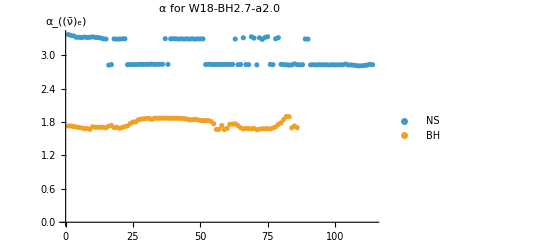

```mathematica
ListPlot[{NScomboData[[All,26]],BHcomboData[[All,26]]},PlotLabel->"α  for W18-BH2.7-a2.0",PlotLegends->{"NS","BH"},AxesLabel->{"","α_((ν̄)_e)"}]
```

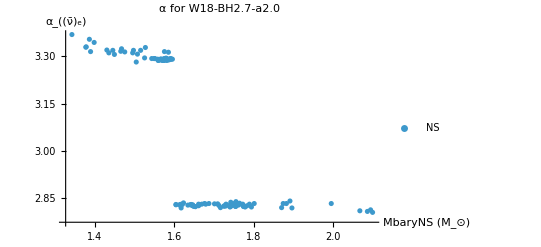

```mathematica
ListPlot[Table[{NScomboData[[i,16]],NScomboData[[i,26]]},{i,1,Length[NScomboData]}],PlotLabel->"α  for W18-BH2.7-a2.0",PlotLegends->{"NS","BH"},AxesLabel->{"MbaryNS (M_⊙)","α_((ν̄)_e)"}]
```

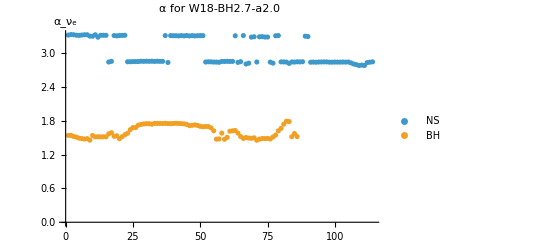

```mathematica
ListPlot[{NScomboData[[All,27]],BHcomboData[[All,27]]},PlotLabel->"α  for W18-BH2.7-a2.0",PlotLegends->{"NS","BH"},AxesLabel->{"","α_ν_e"}]
```

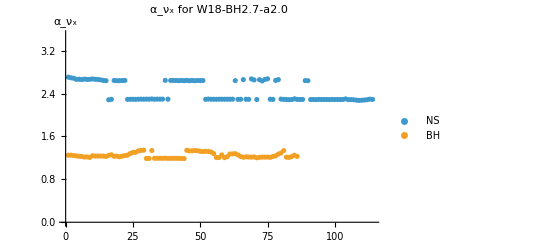

```mathematica
ListPlot[{NScomboData[[All,28]],BHcomboData[[All,28]]},PlotLabel->"α_ν_x for W18-BH2.7-a2.0",PlotLegends->{"NS","BH"},AxesLabel->{"","α_ν_x"},PlotRange->{{0,All},{0,3.5}}]
```

```mathematica
MatrixForm[comboColumns]
```

(1 | Set
2 | M_ZAMS[M_sun]
3 | M_total_precollapse[M_sun]
4 | M_He_core[M_sun]
5 | M_CO_core[M_sun]
6 | M_s=4[M_sun]
7 | mu_4
8 | M_Fe_core[M_sun]
9 | Compactnes_1.5
10 | Compactnes_1.75
11 | Compactnes_2.0
12 | Compactnes_2.25
13 | Compactnes_2.5
14 | {#,Column,1:,ZAMS,mass,(in,units,of,solar,masses)}
15 | {#,Column,2:,compact,remnant,(NS,or,BH)}
16 | {#,Column,3:,M_{NS,b},=,final,baryonic,NS,mass,(in,units,of,solar,masses)}
17 | {#,Column,4:,M_{NS,b}^{lim},=,baryonic,NS,mass,limit,=,baryonic,PNS,mass,at,time,of,BH,formation,(in,units,of,solar,masses)}
18 | {#,Column,5:,t_{exp},=,time,of,explosion,(in,seconds),,defined,as,the,time,when,the,SN,shock,passes,500,km}
19 | {#,Column,6:,t_{BH},=,time,of,BH,formation,(in,seconds)}
20 | {#,Column,7:,E_{nu_ebar}^{tot},/,(10^52,erg),=,total,energy,radiated,in,electron,antineutrinos,("nu_ebar")}
21 | {# Column 8:  E_{nu_e}^{tot} / (10^52 erg) =          --- ",---,electron,neutrinos,("nu_e")}
22 | {# Column 9:  E_{nu_x}^{tot} / (10^52 erg) =          --- ",---,a,representative,species,("nu_x"),of,muon/tau,neutrinos,or,antineutrinos}
23 | {#,Column,10:,<E_{nu_ebar}>,/,MeV,=,mean,neutrino,energy,of,the,time-integrated,nu_ebar,spectrum}
24 | {# Column 11: <E_{nu_e}> / MeV =                   --- ",---,nu_e,spectrum}
25 | {# Column 12: <E_{nu_x}> / MeV =                   --- ",---,nu_x,spectrum}
26 | {#,Column,13:,\overline{alpha}_{nu_ebar},=,spectral-shape,parameter,of,the,time-integrated,nu_ebar,spectrum}
27 | {# Column 14: \overline{alpha}_{nu_e} =                     --- ",---,nu_e,spectrum}
28 | {# Column 15: \overline{alpha}_{nu_x} =                     --- ",---,nu_x,spectrum})

```mathematica
ListPlot[{comboData[[All,20]]*10^52},AxesLabel->{"index","ergs"},PlotLabel->"All Etot (nuebar)"](*MeV*)
```

-Graphics-

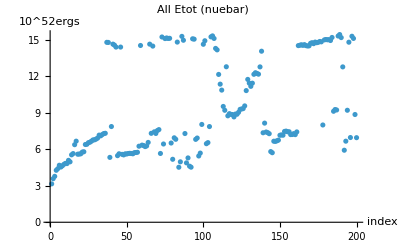

```mathematica
ListPlot[{comboData[[All,20]]},AxesLabel->{"index","10^52ergs"},PlotLabel->"All Etot (nuebar)"](*MeV*)
```

```mathematica
1*erg
```

624151.

```mathematica
Select[comboData,#[[15]]=="BH"&][[All,15]]
```

{BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH,BH}

```mathematica
(*avg Etot for BH*)
avgEtotBH=Mean[Select[comboData,#[[15]]=="BH"&][[All,20]]](*in units of 10^52 ergs*)
```

13.1886

```mathematica
avgEtotBH*10^52*erg(*MeV)*)
```

8.23165×10^58

```mathematica
(*avg Etot for NS*)
avgEtotNS=Mean[Select[comboData,#[[15]]=="NS"&][[All,20]]]
```

6.37464

```mathematica
(*avg Etot for both NS and BH*)
avgEtot=Mean[comboData[[All,20]]](*in units of 10^52 ergs*)
```

9.30463

## finding temperature (avg nu spec)

```mathematica
(*find temperature closest to fiducial case
via equation 8 from Horiuchi et al.2009 https://arxiv.org/abs/0812.3157
and compare to fig 4 therein*)
(*and based on avg neutrino spectrum for fiducial case*)
```

### compare neutrino spectra functions per se

```mathematica
(*find temperature closest to fiducial case

via equation 8 from Horiuchi et al.2009 https://arxiv.org/abs/0812.3157

and compare to fig 4 therein*)
```

make functions of nu energy spectrum

```mathematica
(*from Horiuchi et al. 2021*)
(*used in 2para_DSNB_v19 when computing DSNB flux*)
(*nuetrino spectrum threefold parameterization*)
(*UNLIKE PREVIOUS FUNCTION Etot is NOT in units of Etot/10^52erg*)
(*Etot is in units of Etot/(10^52 erg)*)
(*Eavg is in units of Eavg/MeV*)
(*alpha is dimless*)
(*put all energies in terms of MeV*)
(*as a function of neutrino energy in MeV*)
(*already defined*)
nuSpec2[E_,Etot_,Eavg_,α_]:=((1+α)^(1+α)/Gamma[1+α])*((Etot*10^52*erg)/(Eavg)^2)*((E/Eavg)^α)*Exp[-(1+α)*E/Eavg];
```

```mathematica
(*put all energies in terms of MeV*)
(*as a function of neutrino energy in MeV*)
(*eqn 8 from Horiuchi et al. 2009*) 
(*was not used and depends on neutrino temperature*)
nuSpecDisused[E_,Etot_,Temp_]:=(Etot*10^52*erg)/6*120/(7*Pi^4)*E^2/Temp^4*(Exp[E/Temp]+1)^-1;
```

```mathematica
Manipulate[Plot[{nuSpec2[x,α,Eavg,Etot],nuSpecDisused[x,Etot,T]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All,PlotLegends->{"nu spec with α","nu spec with T"}],{α,2,4},{Eavg,1,20},{Etot,1,20},{T,0.01,10}]
```

```mathematica
Manipulate[Plot[{nuSpec2[x,α,Eavg,Etot],nuSpecDisused[x,Etot,T]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All,PlotLegends->{"nu spec with α","nu spec with T"}],{α,2.2,2.4},{Eavg,1.5,3},{Etot,5,8},{T,0.4,0.7}]
```

### comparison with fiducial avg neutrino spectrum

#### copy-past data

copied and pasted from “2para_DSNB_v19_avgNuSpec.nb”

assumes fiducial case (no MSW, without outliers, etc)

```mathematica
(*avg nu spec for BH*)
(*in units of nuebar energy (MeV) and MeV^-1 spectrum*)
BH2PnuebarAVGwithoutDATA={{0,0.},{1,6.0936674698238165*^54},{2,1.7636528525019653*^55},{3,3.0615665366235736*^55},{4,4.309433128194418*^55},{5,5.406993345130638*^55},{6,6.307940580520162*^55},{7,6.998535068804463*^55},{8,7.484530264615871*^55},{9,7.782806686385286*^55},{10,7.915942173268147*^55},{11,7.908704699758968*^55},{12,7.785834318191241*^55},{13,7.570697609627535*^55},{14,7.284532200230562*^55},{15,6.946086551920675*^55},{16,6.571519561117686*^55},{17,6.174465585253406*^55},{18,5.766199383470264*^55},{19,5.355855906982512*^55},{20,4.95067441152541*^55},{21,4.556246694292664*^55},{22,4.176756569007798*^55},{23,3.8152028277794725*^55},{24,3.4736015019427313*^55},{25,3.153165664071894*^55},{26,2.8544626285639857*^55},{27,2.577549441430925*^55},{28,2.322088171349876*^55},{29,2.0874428478205832*^55},{30,1.8727600288808257*^55},{31,1.6770349857172965*^55},{32,1.4991654117587887*^55},{33,1.3379944329638786*^55},{34,1.1923445375489135*^55},{35,1.061043873566166*^55},{36,9.429461924327034*^54},{37,8.369455527746303*^54},{38,7.419867460810713*^54},{39,6.570722660053692*^54},{40,5.812665177075642*^54}};
```

```mathematica
(*avg nu spec for NS*)
NS2PnuebarAVGwithoutDATA={{0,0.},{1,1.644198097172308*^54},{2,9.49834938240605*^54},{3,2.387109927166062*^55},{4,4.2587943464413044*^55},{5,6.292480886296024*^55},{6,8.248842759479949*^55},{7,9.95416874852778*^55},{8,1.1304124819593816*^56},{9,1.2254138272310572*^56},{10,1.2805051180012132*^56},{11,1.2988602415021418*^56},{12,1.2854871336079573*^56},{13,1.2462432824480958*^56},{14,1.1871234544425291*^56},{15,1.1137856044175939*^56},{16,1.0312681730025585*^56},{17,9.438513445231604*^55},{18,8.550201168328068*^55},{19,7.674945862113992*^55},{20,6.833006703093526*^55},{21,6.038615745803112*^55},{22,5.300962389126869*^55},{23,4.625156999219973*^55},{24,4.0131186117776903*^55},{25,3.4643574468251276*^55},{26,2.9766408884790757*^55},{27,2.546543387980288*^55},{28,2.169887992465287*^55},{29,1.8420911641677248*^55},{30,1.5584242465935523*^55},{31,1.314205127633038*^55},{32,1.1049329149206438*^55},{33,9.263771840700171*^54},{34,7.746318674513738*^54},{35,6.461423063648503*^54},{36,5.377125092684141*^54},{37,4.4649830976257995*^54},{38,3.6999093253730974*^54},{39,3.0599446284490614*^54},{40,2.5259987029598854*^54}};
```

```mathematica
bothNSBHnuebarAVGwithoutDat=Table[{NS2PnuebarAVGwithoutDATA[[i,1]],NS2PnuebarAVGwithoutDATA[[i,2]]+BH2PnuebarAVGwithoutDATA[[i,2]]},{i,1,Length[BH2PnuebarAVGwithoutDATA]}]
```

{{0,0.},{1,7.73787×10^54},{2,2.71349×10^55},{3,5.44868×10^55},{4,8.56823×10^55},{5,1.16995×10^56},{6,1.45568×10^56},{7,1.69527×10^56},{8,1.87887×10^56},{9,2.00369×10^56},{10,2.0721×10^56},{11,2.08973×10^56},{12,2.06407×10^56},{13,2.00331×10^56},{14,1.91558×10^56},{15,1.80839×10^56},{16,1.68842×10^56},{17,1.5613×10^56},{18,1.43164×10^56},{19,1.30308×10^56},{20,1.17837×10^56},{21,1.05949×10^56},{22,9.47772×10^55},{23,8.44036×10^55},{24,7.48672×10^55},{25,6.61752×10^55},{26,5.8311×10^55},{27,5.12409×10^55},{28,4.49198×10^55},{29,3.92953×10^55},{30,3.43118×10^55},{31,2.99124×10^55},{32,2.6041×10^55},{33,2.26437×10^55},{34,1.96698×10^55},{35,1.70719×10^55},{36,1.48066×10^55},{37,1.28344×10^55},{38,1.11198×10^55},{39,9.63067×10^54},{40,8.33866×10^54}}

#### Plots (eye-balling)

```mathematica
NSBHavgNuSpecPlot=ListPlot[{BH2PnuebarAVGwithoutDATA,NS2PnuebarAVGwithoutDATA,bothNSBHnuebarAVGwithoutDat},Joined->True,Frame->{{True, False}, {True, False}},FrameLabel->{"E_ν (MeV)","spectrum (MeV^-1)"},PlotLegends->{"BH","NS","both"}]
```

-Graphics-

```mathematica
(*make interpolation functions*)
BHavgNuSpecFunc=Interpolation[BH2PnuebarAVGwithoutDATA];
NSavgNuSpecFunc=Interpolation[NS2PnuebarAVGwithoutDATA];
bothNSBHnuSpecFunc=Interpolation[bothNSBHnuebarAVGwithoutDat];
```

all

```mathematica
Manipulate[Plot[{BHavgNuSpecFunc[x],NSavgNuSpecFunc[x],nuSpecDisused[x,Etot,T]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All,PlotLegends->{"BH","NS","nu spec with T"}],{Etot,1,100},{T,0.01,10}]
```

```mathematica
Manipulate[Plot[{bothNSBHnuSpecFunc[x],BHavgNuSpecFunc[x],NSavgNuSpecFunc[x],nuSpecDisused[x,Etot,T]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All,PlotLegends->{"Both","BH","NS","nu spec with T"}],{Etot,40,50},{T,4,6}]
```

close to NS

```mathematica
Manipulate[Plot[{BHavgNuSpecFunc[x],NSavgNuSpecFunc[x],nuSpecDisused[x,Etot,T]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All,PlotLegends->{"BH","NS","nu spec with T"}],{Etot,30,40},{T,4,6}]
```

close to BH

```mathematica
Manipulate[Plot[{BHavgNuSpecFunc[x],NSavgNuSpecFunc[x],nuSpecDisused[x,Etot,T]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All,PlotLegends->{"BH","NS","nu spec with T"}],{Etot,20,22},{T,4.5,6}]
```

#### Attempt (Failed) with fixed avg Etot

try fixing Etot to average value (FAILED)

```mathematica
Manipulate[Plot[{NSavgNuSpecFunc[x],nuSpecDisused[x,avgEtotNS,T]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All,PlotLegends->{"NS","nu spec with T"}],{T,0.01,10}]
```

```mathematica
Manipulate[Plot[{BHavgNuSpecFunc[x],nuSpecDisused[x,avgEtotBH,T]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All,PlotLegends->{"BH","nu spec with T"}],{T,0.01,10}]
```

```mathematica
Manipulate[Plot[{bothNSBHnuSpecFunc[x],nuSpecDisused[x,avgEtot,T]},{x,Emin,Emax},AxesLabel->{"MeV","MeV^-1"},PlotRange->All,PlotLegends->{"BH+NS","nu spec with T"}],{T,0.01,10}]
```

### attempt to fit

for NS

```mathematica
(*for NS and BH and both BH+NS*)
(*in format of {a->fittedEtot,b->fittedT}*)
fitNS=FindFit[NS2PnuebarAVGwithoutDATA,nuSpecDisused[x,a,b],{a,b},x]
fitBH=FindFit[BH2PnuebarAVGwithoutDATA,nuSpecDisused[x,a,b],{a,b},x]
fitboth=FindFit[bothNSBHnuebarAVGwithoutDat,nuSpecDisused[x,a,b],{a,b},x]
```

{a→32.8562,b→4.82554}

{a→23.4369,b→4.99796}

{a→56.1175,b→4.88599}

```mathematica
fitNS[[1,2]]
```

32.8562

```mathematica
(*make tables for fitted data*)
(*coincides with indep energy values in data*)
(*for NS, for BH, for both NS+BH*)
fitNSlist=Table[{i,nuSpecDisused[i,fitNS[[1,2]],fitNS[[2,2]]]},{i,NS2PnuebarAVGwithoutDATA[[All,1]]}];
fitBHlist=Table[{i,nuSpecDisused[i,fitBH[[1,2]],fitBH[[2,2]]]},{i,NS2PnuebarAVGwithoutDATA[[All,1]]}];
fitbothlist=Table[{i,nuSpecDisused[i,fitboth[[1,2]],fitboth[[2,2]]]},{i,NS2PnuebarAVGwithoutDATA[[All,1]]}];
```

```mathematica
(*legend maker*)
legendMaker[x_,y_]:="E_tot="<>ToString[x]<>"x10^52erg "<>"T="<>ToString[y]<>" MeV"
```

```mathematica
legendMaker[fitNS[[1,2]],fitNS[[2,2]]]
```

E_tot=32.8562x10^52erg T=4.82554 MeV

```mathematica
nuSpecFiducialFitPlot=ListPlot[{BH2PnuebarAVGwithoutDATA,NS2PnuebarAVGwithoutDATA,bothNSBHnuebarAVGwithoutDat,fitNSlist,fitBHlist,fitbothlist},Joined->True,Frame->{{True, False}, {True, False}},FrameLabel->{"E_ν (MeV)","dN/dE (MeV^-1)"},
PlotLegends->{"BH","NS","both",legendMaker[fitNS[[1,2]],fitNS[[2,2]]],legendMaker[fitBH[[1,2]],fitBH[[2,2]]],legendMaker[fitboth[[1,2]],fitboth[[2,2]]]}
,PlotStyle->{{defaultColor[[1]]},defaultColor[[2]],defaultColor[[3]],{Purple,Dashed},{Red,Dotted},{Blue,DotDashed}}]
```

-Graphics-

```mathematica
defaultColor
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(*Export["nuSpecFiducialFitPlot.pdf",nuSpecFiducialFitPlot];*)
```

## finding temperature (dsnb flux)

copy DSNB flux for fiducial case

```mathematica
(*copy and pasted from dsnbDataReader version 8*)
(*fiducial DSNB flux*)
fiducialDSNBflux={{0.,0.},{0.25,0.13065587623888678},{0.5,0.4578637688373941},{0.75,0.9255830748863898},{1.,1.473501752951212},{1.25,2.0480195776204875},{1.5,2.60772285700208},{1.75,3.123774954923733},{2.,3.5785375332459566},{2.25,3.9632533599553224},{2.5,4.275634370250243},{2.75,4.517781946412638},{3.,4.694538692799748},{3.25,4.811497508713607},{3.5,4.876156671448356},{3.75,4.897075663609658},{4.,4.879820779770396},{4.25,4.83065881194319},{4.5,4.755247151976035},{4.75,4.6585999529275925},{5.,4.545098882887377},{5.25,4.418530152355565},{5.5,4.282135354834558},{5.75,4.138667938608967},{6.,3.9904501622478374},{6.25,3.8394274806396185},{6.5,3.6872187137119994},{6.75,3.5351612637372383},{7.,3.384351218479074},{7.25,3.2356785159500734},{7.5,3.0898575307097254},{7.75,2.9474535264573545},{8.,2.8089054429098788},{8.25,2.6745454719460513},{8.5,2.544615845353931},{8.75,2.4192832148105534},{9.,2.298650960438508},{9.25,2.182769721197339},{9.5,2.071646400494929},{9.75,1.965251864655896},{10.,1.8635275205010329},{10.25,1.7663909311308374},{10.5,1.6737406057237363},{10.75,1.5854600793258298},{11.,1.5014213817757143},{11.25,1.4214879806467793},{11.5,1.3455172710110341},{11.75,1.2733626745904985},{12.,1.2048754021695864},{12.25,1.1399059257447346},{12.5,1.0783052005758895},{12.75,1.0199256719035472},{13.,0.964622096459725},{13.25,0.9122522049113797},{13.5,0.8578255406469625},{13.75,0.8157623056086489},{14.,0.7714024083905223},{14.25,0.7294426834650212},{14.5,0.6897390330202667},{14.75,0.6522002557757668},{15.,0.6167141725954278},{15.25,0.5831733373769765},{15.5,0.5514750020095487},{15.75,0.5215210525861075},{16.,0.4932179223039638},{16.25,0.46647648572691225},{16.5,0.44121193841852846},{16.75,0.4173436653763184},{17.,0.3947951011903535},{17.25,0.37349358440887515},{17.5,0.3533702082091793},{17.75,0.3325039905025251},{18.,0.314620062831106},{18.25,0.29772679932172713},{18.5,0.28176872239616496},{18.75,0.26669337396480086},{19.,0.2539471284449983},{19.25,0.24042508664665524},{19.5,0.22764711644019447},{19.75,0.2155714490670836},{20.,0.20415864513116203},{20.25,0.1933714731235},{20.5,0.18317479283495958},{20.75,0.17353544368300247},{21.,0.16448223557271247},{21.25,0.1558611772031078},{21.5,0.14770904541347038},{21.75,0.13999957243926314},{22.,0.1327079828061729},{22.25,0.12581091002348674},{22.5,0.11894282183055566},{22.75,0.11280059217701897},{23.,0.10698792149089176},{23.25,0.10148651625292268},{23.5,0.09627912493243446},{23.75,0.09134947807427923},{24.,0.08668223173957154},{24.25,0.0822629141344543},{24.5,0.07807787526564851},{24.75,0.0741532750134429},{25.,0.07039737404849164},{25.25,0.06683929873969516},{25.5,0.06346824093132487},{25.75,0.06027400221157299},{26.,0.057246958686717885},{26.25,0.05437802780478049},{26.5,0.05165863711301775},{26.75,0.04908069483930304},{27.,0.04663656219300213},{27.25,0.04403653500947571},{27.5,0.04185493373271746},{27.75,0.0397858461582883},{28.,0.03782323716360744},{28.25,0.03596140748656826},{28.5,0.03419497442174425},{28.75,0.03251885365277403},{29.,0.030928242153581836},{29.25,0.029418602094966634},{29.5,0.027985645696770506},{29.75,0.02662532096932671},{30.,0.025333798291189414},{30.25,0.024107457773273746},{30.5,0.0229428773624874},{30.75,0.021836821640724972},{31.,0.020786231277727923},{31.25,0.019788213098795776},{31.5,0.018840030730672665},{31.75,0.01793909579113797},{32.,0.01708295958990319},{32.25,0.016269305310370578},{32.5,0.01549594064364533},{32.75,0.014760790847920464},{33.,0.014061892207977813},{33.25,0.013397385871074256},{33.5,0.01276551203691768},{33.75,0.012164604480783743},{34.,0.011593085390091237},{34.25,0.011049460495942286},{34.5,0.010532314482250742},{34.75,0.010040306656130163},{35.,0.009572166864197863},{35.25,0.009126691640375406},{35.5,0.008702740571634312},{35.75,0.008299232868950164},{36.,0.007915144131493523},{36.25,0.00754950329280412},{36.5,0.007201389738369092},{36.75,0.006869930584658967},{37.,0.00655429811026949},{37.25,0.006253707330375285},{37.5,0.005967413706225389},{37.75,0.0056947109819025015},{38.,0.005434929141029893},{38.25,0.005187432476543626},{38.5,0.004951617767055273},{38.75,0.004726912553712909},{39.,0.004512773511827591},{39.25,0.0043086849118702825},{39.5,0.0041141571647611876},{39.75,0.003928725446671694},{40.,0.0037519483988389555}};
```

interpolate DSNB flux for fiducial case

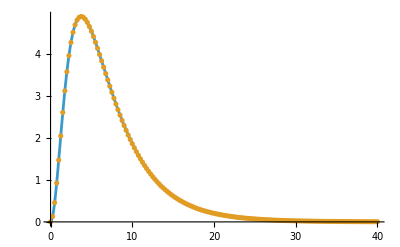

```mathematica
dsnbFluxFidFunc=Interpolation[fiducialDSNBflux];
(*confirm it works*)
Show[Plot[dsnbFluxFidFunc[x],{x,0,40}],ListPlot[fiducialDSNBflux,PlotStyle->defaultColor[[2]]]]
```

fit DSNB flux to generic fermi dirac distribution

```mathematica
(*generic fermi dirac distribution*)
(*take in neutrino energy and temperature in MeV*)
fermiDirac1[E_,T_,A_]:=A/(Exp[E/T]+1)
```

```mathematica
Manipulate[Plot[{fermiDirac1[x,T,A],fermiDirac1[x,T*2,A*2],fermiDirac1[x,T/2,A/2],fermiDirac1[x,T/2,A*2],fermiDirac1[x,T*2,A/2]},{x,0,40},AxesLabel->{"MeV","MeV^-1cm^-2,s^-1"},PlotRange->All,PlotLegends->{"FD","FD high T high A","FD low T low A","FD low T high A","FD high T low A"}],{T,0.01,10},{A,0.01,30}]
```

```mathematica
Manipulate[Plot[{fermiDirac1[x,T,A],dsnbFluxFidFunc[x]},{x,0,40},AxesLabel->{"MeV","MeV^-1cm^-2,s^-1"},PlotRange->All,PlotLegends->{"Fermi-Dirac","Fiducial DSNB Flux"}],{T,0.01,10},{A,0.01,30}]
```

```mathematica
Manipulate[Plot[{fermiDirac1[x,T,A],dsnbFluxFidFunc[x]},{x,0,40},AxesLabel->{"MeV","MeV^-1cm^-2,s^-1"},PlotRange->All,PlotLegends->{"Fermi-Dirac","Fiducial DSNB Flux"}],{T,4.8,5.0},{A,16,17}]
```

```mathematica
Manipulate[Plot[{fermiDirac1[x,T,A],dsnbFluxFidFunc[x]},{x,0,40},AxesLabel->{"MeV","MeV^-1cm^-2,s^-1"},PlotRange->All,PlotLegends->{"Fermi-Dirac","Fiducial DSNB Flux"}],{T,0.01,10},{A,0.01,30}]
```

find fit attempt 1

```mathematica
dsnbFluxFitPara=FindFit[fiducialDSNBflux,fermiDirac1[x,a,b],{a,b},x]
```

{a→7.93766,b→8.08467}

```mathematica
dsnbFluxFitPara[[1,2]]
dsnbFluxFitPara[[2,2]]
```

7.93766

8.08467

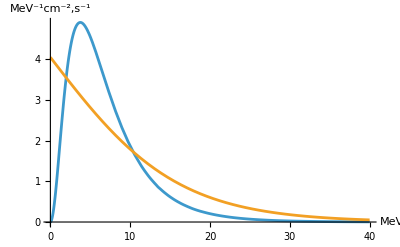

```mathematica
Plot[{dsnbFluxFidFunc[x],fermiDirac1[x,dsnbFluxFitPara[[1,2]],dsnbFluxFitPara[[2,2]]]},{x,0,40},AxesLabel->{"MeV","MeV^-1cm^-2,s^-1"}]
```

fit attempt 2

```mathematica
maxIndex=Position[fiducialDSNBflux[[All,2]],Max[fiducialDSNBflux[[All,2]]]][[1,1]]
```

16

```mathematica
fiducialDSNBflux[[maxIndex]]
```

{3.75,4.89708}

```mathematica
fiducialDSNBflux[[maxIndex;;Length[fiducialDSNBflux]]]
```

{{3.75,4.89708},{4.,4.87982},{4.25,4.83066},{4.5,4.75525},{4.75,4.6586},{5.,4.5451},{5.25,4.41853},{5.5,4.28214},{5.75,4.13867},{6.,3.99045},{6.25,3.83943},{6.5,3.68722},{6.75,3.53516},{7.,3.38435},{7.25,3.23568},{7.5,3.08986},{7.75,2.94745},{8.,2.80891},{8.25,2.67455},{8.5,2.54462},{8.75,2.41928},{9.,2.29865},{9.25,2.18277},{9.5,2.07165},{9.75,1.96525},{10.,1.86353},{10.25,1.76639},{10.5,1.67374},{10.75,1.58546},{11.,1.50142},{11.25,1.42149},{11.5,1.34552},{11.75,1.27336},{12.,1.20488},{12.25,1.13991},{12.5,1.07831},{12.75,1.01993},{13.,0.964622},{13.25,0.912252},{13.5,0.857826},{13.75,0.815762},{14.,0.771402},{14.25,0.729443},{14.5,0.689739},{14.75,0.6522},{15.,0.616714},{15.25,0.583173},{15.5,0.551475},{15.75,0.521521},{16.,0.493218},{16.25,0.466476},{16.5,0.441212},{16.75,0.417344},{17.,0.394795},{17.25,0.373494},{17.5,0.35337},{17.75,0.332504},{18.,0.31462},{18.25,0.297727},{18.5,0.281769},{18.75,0.266693},{19.,0.253947},{19.25,0.240425},{19.5,0.227647},{19.75,0.215571},{20.,0.204159},{20.25,0.193371},{20.5,0.183175},{20.75,0.173535},{21.,0.164482},{21.25,0.155861},{21.5,0.147709},{21.75,0.14},{22.,0.132708},{22.25,0.125811},{22.5,0.118943},{22.75,0.112801},{23.,0.106988},{23.25,0.101487},{23.5,0.0962791},{23.75,0.0913495},{24.,0.0866822},{24.25,0.0822629},{24.5,0.0780779},{24.75,0.0741533},{25.,0.0703974},{25.25,0.0668393},{25.5,0.0634682},{25.75,0.060274},{26.,0.057247},{26.25,0.054378},{26.5,0.0516586},{26.75,0.0490807},{27.,0.0466366},{27.25,0.0440365},{27.5,0.0418549},{27.75,0.0397858},{28.,0.0378232},{28.25,0.0359614},{28.5,0.034195},{28.75,0.0325189},{29.,0.0309282},{29.25,0.0294186},{29.5,0.0279856},{29.75,0.0266253},{30.,0.0253338},{30.25,0.0241075},{30.5,0.0229429},{30.75,0.0218368},{31.,0.0207862},{31.25,0.0197882},{31.5,0.01884},{31.75,0.0179391},{32.,0.017083},{32.25,0.0162693},{32.5,0.0154959},{32.75,0.0147608},{33.,0.0140619},{33.25,0.0133974},{33.5,0.0127655},{33.75,0.0121646},{34.,0.0115931},{34.25,0.0110495},{34.5,0.0105323},{34.75,0.0100403},{35.,0.00957217},{35.25,0.00912669},{35.5,0.00870274},{35.75,0.00829923},{36.,0.00791514},{36.25,0.0075495},{36.5,0.00720139},{36.75,0.00686993},{37.,0.0065543},{37.25,0.00625371},{37.5,0.00596741},{37.75,0.00569471},{38.,0.00543493},{38.25,0.00518743},{38.5,0.00495162},{38.75,0.00472691},{39.,0.00451277},{39.25,0.00430868},{39.5,0.00411416},{39.75,0.00392873},{40.,0.00375195}}

fit only the max and beyond

```mathematica
dsnbFluxFitPara2=FindFit[fiducialDSNBflux[[maxIndex;;Length[fiducialDSNBflux]]],fermiDirac1[x,a,b],{a,b},x]
```

{a→4.71056,b→17.4157}

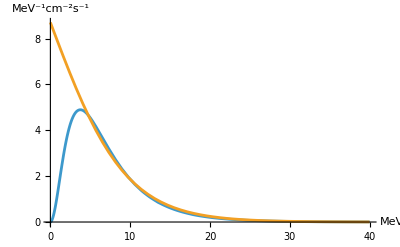

```mathematica
Plot[{dsnbFluxFidFunc[x],fermiDirac1[x,dsnbFluxFitPara2[[1,2]],dsnbFluxFitPara2[[2,2]]]},{x,0,40},AxesLabel->{"MeV","MeV^-1cm^-2s^-1"}]
```

fit below max

```mathematica
dsnbFluxFitPara7=FindFit[fiducialDSNBflux[[1;;maxIndex]],fermiDirac1[x,a,b],{a,b},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→3.10574×10^15,b→5.7977}

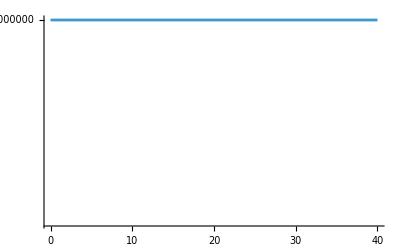

```mathematica
Plot[fermiDirac1[x,3*10^15,5.8],{x,0,40}]
```

#### fit to fermi dirac nu spec from Horiuchi et al. 2008

only max and beyond

```mathematica
dsnbFluxFitPara3=FindFit[fiducialDSNBflux[[maxIndex;;Length[fiducialDSNBflux]]],nuSpecDisused[x,a,b],{a,b},x]
```

{a→2.3051×10^-55,b→2.11472}

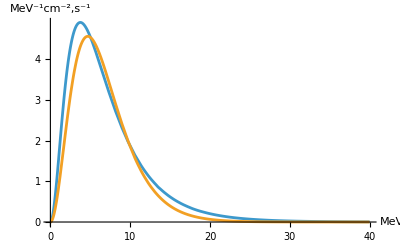

```mathematica
Plot[{dsnbFluxFidFunc[x],nuSpecDisused[x,dsnbFluxFitPara3[[1,2]],dsnbFluxFitPara3[[2,2]]]},{x,0,40},AxesLabel->{"MeV","MeV^-1cm^-2,s^-1"}]
```

entire flux

```mathematica
dsnbFluxFitPara4=FindFit[fiducialDSNBflux,nuSpecDisused[x,a,b],{a,b},x]
```

{a→0.,b→1.}

only below max

```mathematica
dsnbFluxFitPara3=FindFit[fiducialDSNBflux[[1;;maxIndex]],nuSpecDisused[x,a,b],{a,b},x]
```

{a→1.33875×10^-55,b→1.56153}

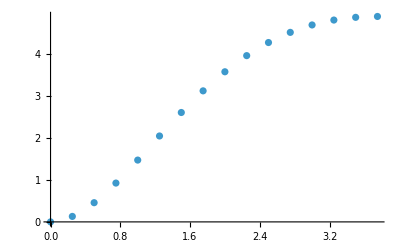

```mathematica
ListPlot[fiducialDSNBflux[[1;;maxIndex]]]
```

#### attempt with maxwell boltzman distribution

```mathematica
PDF[MaxwellDistribution[σ],x]
```

Piecewise[{{(ⅇ^(-x^2/(2 σ^2)) √(2/π) x^2)/σ^3, x>0}, {0, True}}]

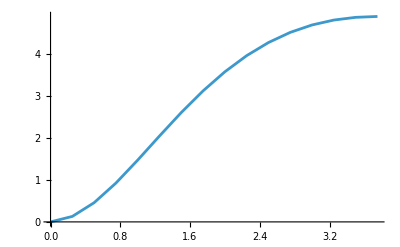

```mathematica
ListPlot[fiducialDSNBflux[[1;;maxIndex]],Joined->True]
```

```mathematica
dsnbFluxFitPara4=FindFit[fiducialDSNBflux[[1;;maxIndex]],PDF[MaxwellDistribution[σ],x],{σ},x]
```

{σ→1.50077}

```mathematica
dsnbFluxFitPara4[[1,2]]
```

1.50077

```mathematica
maxwellTab=Table[{x,PDF[MaxwellDistribution[dsnbFluxFitPara4[[1,2]]],x]},{x,0,4,0.01}];
Length[maxwellTab]
```

401

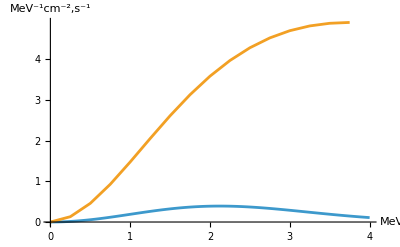

```mathematica
ListPlot[{maxwellTab,fiducialDSNBflux[[1;;maxIndex]]},Joined->True,AxesLabel->{"MeV","MeV^-1cm^-2,s^-1"},PlotRange->All]
```

#### attempt to fit to sigmoid

```mathematica
LogisticSigmoid[2.]
```

0.880797

```mathematica
sigmoid[x_,a_,b_]=b/(1+Exp[-x/a])
```

b/(1+ⅇ^(-x/a))

```mathematica
dsnbFluxFitPara5=FindFit[fiducialDSNBflux[[1;;maxIndex]],sigmoid[x,a,b],{a,b},x]
```

{a→1.14183,b→3.91432}

```mathematica
fiducialDSNBflux[[maxIndex]]
```

{3.75,4.89708}

```mathematica
dsnbFluxFitPara5[[1,2]]
dsnbFluxFitPara5[[2,2]]
```

1.14183

3.91432

```mathematica
sigmoidTab=Table[{x,sigmoid[x,dsnbFluxFitPara5[[1,2]],dsnbFluxFitPara5[[2,2]]]},{x,0,3.75}]
```

{{0,1.95716},{1,2.76331},{2,3.3356},{3,3.65051}}

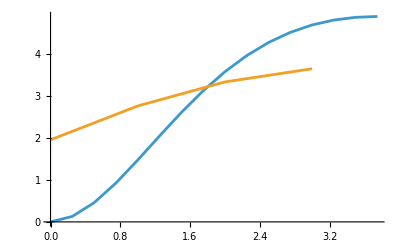

```mathematica
ListPlot[{fiducialDSNBflux[[1;;maxIndex]],sigmoidTab},Joined->True]
```

#### attempt to modified sigmoid

```mathematica
modsigmoid[x_,a_,b_]=x^b/(1+Exp[-x/a])
```

x^b/(1+ⅇ^(-x/a))

```mathematica
dsnbFluxFitPara6=FindFit[fiducialDSNBflux[[1;;maxIndex]],modsigmoid[x,a,b],{a,b},x]
```

FindFit::nrjnum: The Jacobian is not a matrix of real numbers at {a,b} = {1.,1.}.

{a→1.,b→1.}

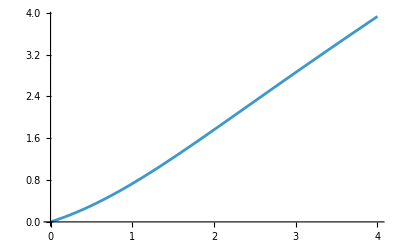

```mathematica
Plot[modsigmoid[x,1,1],{x,0,4}]
```

```mathematica
modsigmoidTab=Table[{x,modsigmoid[x,1,1]},{x,0,4}]
```

{{0,0},{1,1/(1+1/ⅇ)},{2,2/(1+1/ⅇ^2)},{3,3/(1+1/ⅇ^3)},{4,4/(1+1/ⅇ^4)}}

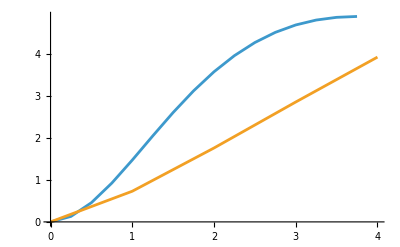

```mathematica
ListPlot[{fiducialDSNBflux[[1;;maxIndex]],modsigmoidTab},Joined->True]
```